# Final Project

## Eura Shin and Nolan Hughes

## Basics

## Set Directory

```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\WKUUSER\Dropbox\Final Prjoect Random\Final Presentation Shit\HughesShinFinalCPSReport\HughesShinFinalCodeFolder

## Variables

### Time Variables

```mathematica
hoursT=7;
minutesT=00;
pmDetect=0;
currentDay=1;
```

### User Inventory Variables

```mathematica
userPrices={1,1,1};
userHas={0,0,0,0,0,0};
milkSugarCoffee={0,0,0};
iceStrawberries={0,0};
teaBags=0;
spoilingList={{},{},{},{},{},{}};
spoiledList={{},{},{},{},{},{}};
```

### Ugrade Store Variables

```mathematica
storeName="";
wifiBoolean=False;
adList={0};
numOfEmployees=2;
storeLayoutsList=
{Import["Store Layouts/Store Layout 1.png"],Import["Store Layouts/Store Layout 2.png"],Import["Store Layouts/Store Layout 3.png"]};
storeLayout=storeLayoutsList[[1]];
wifiCost=1 ;(*Wifi cost approximately $30 a month we decrement $1 a day because the average month is 30 days*)
color=Lighter[Brown];
layoutsList={1,storeLayout};
adCosts={5.25,18.50,175};
```

### Customer Data Variables

```mathematica
coffeeCupsData={};teaCupsData={};smoothieCupsData={};coffeeCupsHourly={};
teaCupsHourly={};
smoothieCupsHourly={};
```

### Expense and Money Variables

```mathematica
storeLayoutCount=1;
totalExpenses={};
individualExpenses={};
totalProfit={};
currentMoneyList={};
```

### Demographics Variables

```mathematica
frankfortPic=ImageResize[Import["Pictures/frankfort.jpg"],200];
losAngelesPic=ImageResize[Import["Pictures/LA.jpg"],{200,160}];
tallahasseePic=ImageResize[Import["Pictures/tallahassee.jpg"],200];
location=frankfortList;
```

### Starting Money Variables

```mathematica
frankfortMoney={150,500,1000,2000};
losAngelesMoney={15000,50000,100000,200000};
tallahasseeMoney={750,2500,5000,10000};
moneyLocationList={frankfortMoney,losAngelesMoney,tallahasseeMoney};
```

### Customer Satisfaction Varibles

```mathematica
cSat={1,1,1};
customersWhoDidVisit={};
```

### Location Related Variables

```mathematica
laSuggest={50,60,70,80,90,100,110,120,130,140,150,160,170,180,190,200,210,220,230,240,250,260,270,280,290,300,310,320,330,340,350,360,370,380,390,400,410,420,430,440,450,460,470,480,490,500,510,520,530,540,550,560,570,580,590,600,610,620,630,640,650,660,670,680,690,700};
tallahasseeSuggest={50,60,70,80,90,100,110,120,130,140,150,160,170,180,190,200,210,220,230,240,250,260,270,280,290,300,310,320,330,340,350,360,370,380,390,400,410,420,430,440,450};
frankfortSuggest={10,20,30,40,50,60,70,80,90,100,110,120,130,140,150,160,170,180,190,200,210,220,230,240,250,260,270,280,290,300};
```

## Variable Explanations

milkSugarCoffee, teaBags, and iceStrawberries is the amount of ingredients that the user chooses to put into one cup.
milkSugarCoffee= {cups of milk, teaspoons of sugar, tablespoons of coffee} in one cup of coffee.
teaBags= number of teaBags in each cup.
iceStrawberries= {cups of ice, cups of strawberries} in one serving of smoothie.

## Demographics

```mathematica
(*Data about the demographics of our chosen location options that has been collected from various sources. Refer to: Sources list*)
frankfortList=ReadList["Price Data/frankfort demographics.txt",Expression];
losAngelesList=ReadList["Price Data/los angeles demographics.txt",Expression];
tallahasseeList=ReadList["Price Data/tallahassee demographics.txt",Expression];
```

```mathematica
(*takes the given information from a location and assigns to global variables*)
uFindLocation[list_]:=
Module[{},
drinkingPerentages=list[[1]];
population=list[[2]];
agePercentages=list[[3]];
agePops=list[[3]]*list[[2]];
popPercentDrinkers=(list[[3]]*list[[2]])*list[[1]];
numberOfStores=list[[4]];
]
```

## Functions

## Customer Satisfaction Functions

### Customer Satisfaction Calculation

```mathematica
(*this function takes the number of customers will visit and how many products you can make and calculates the customers satisfaction ratios based of the difference*)
cSatCheck[]:=
Module[{cupsC=Total[coffeeCupsHourly],cupsT=Total[teaCupsHourly],cupsS=Total[smoothieCupsHourly],actualMade},
(*find the actual cups the user can make*)
actualMade=todayUserCanMake[milkSugarCoffee,teaBags,iceStrawberries,userHas];

(*Check coffee customers*)
If[actualMade[[1]]<cupsC,
(*then*)
cSat[[1]]-=((cupsC-actualMade[[1]])/1200),
(*else*)
cSat[[1]]+=.0476
];
If[cSat[[1]]>1.2,
(*then*)
cSat[[1]]=1.2];

(*Check tea customers*)
If[actualMade[[2]]<cupsT,
(*then*)
cSat[[2]]-=((cupsT-actualMade[[2]])/1200),
(*else*)
cSat[[2]]+=.0476
];
If[cSat[[2]]>1.1,
(*then*)
cSat[[2]]=1.1];

(*Check smoothie customers*)
If[actualMade<cupsS,
(*then*)
cSat[[3]]-=((cupsS-actualMade[[3]])/1200),
(*else*)
cSat[[3]]+=.0476
];
If[cSat[[3]]>1.1,
(*then*)
cSat[[3]]=1.1];
]
```

## Employee Button Bars

### Frankfort Button Bar

```mathematica
(*employee selcetion for frankfort*)
frankfortEmployeesBar=RadioButtonBar[
Dynamic[numOfEmployees],
{2-> 2,3-> 3,4-> 4,5-> 5}
];
```

### LA Button Bar

```mathematica
(*employee selcetion for Los Angeles*)
losAngelesEmployeesBar=RadioButtonBar[
Dynamic[numOfEmployees],
{2-> 2,5-> 5,8-> 8,10-> 10}
];
```

### Tallahassee Button Bar

```mathematica
(*employee selcetion for tallahassee*)
tallahasseeEmployeesBar=RadioButtonBar[
Dynamic[numOfEmployees],
{2-> 2,4-> 4,6-> 6,8-> 8}
];
```

### Button Bar Switch

```mathematica
(*this function returns the proper employees selection when given the location*)
employeeButtons[loc_]:=
Switch[loc,frankfortList,frankfortEmployeesBar,tallahasseeList,tallahasseeEmployeesBar,losAngelesList,losAngelesEmployeesBar]
```

## Weather and Season Functions

```mathematica
(*Function that will determine the season based on the given month*)
uFindSeason[date_]:=
Module[{modded},
modded=Mod[date,12];
If[
modded≥0&&modded≤2,Return["Winter"],
If[
modded≥3&&modded≤5, Return["May"],
If[modded≥6&&modded≤8,Return["Summer"],
Return["Fall"]
];
];
];
]
```

```mathematica
(*this is a function that will take in the current season and return a weather condition for the following day. Options are: Sunny, Cloudy, Humid, Rainy, Snowy*)
uChangeWeather[currentSeason_]:=
Module[{weatherList={},i,weatherToday},
(*setting the season*)
If[SameQ[currentSeason,"Spring"], (*weather more suited for spring*)
For[i=1,i≤15,i++,AppendTo[weatherList,"Rainy"];]; (*15/50 chance of rain*)
For[i=1,i≤14,i++,AppendTo[weatherList,"Cloudy"];]; (*14/50 chance of cloudy*)
For[i=1,i≤1,i++,AppendTo[weatherList,"Snowy"];]; (*1/50 chance of snowy*)
For[i=1,i≤5,i++,AppendTo[weatherList,"Humid"];]; (*10/50 chance of humid*)
For[i=1,i≤15,i++,AppendTo[weatherList,"Sunny"];]; (*10/50 chance of sunny*)
,
If[SameQ[currentSeason,"Summer"], (*weather more suited for Summer*)
For[i=1,i≤7,i++,AppendTo[weatherList,"Rainy"];]; (*7/50 chance of rain*)
For[i=1,i≤6,i++,AppendTo[weatherList,"Cloudy"];]; (*6/50 chance of cloudy*)
For[i=1,i≤7,i++,AppendTo[weatherList,"Humid"];]; (*7/50 chance of humid*)
For[i=1,i≤30,i++,AppendTo[weatherList,"Sunny"];]; (*30/50 chance of sunny*)
,
If[SameQ[currentSeason,"Winter"], (*weather more suited for Winter*)
For[i=1,i≤15,i++,AppendTo[weatherList,"Cloudy"];]; (*15/50 chance of cloudy*)
For[i=1,i≤5,i++,AppendTo[weatherList,"Sunny"];]; (*5/50 chance of humid*)
For[i=1,i≤30,i++,AppendTo[weatherList,"Snowy"];]; (*30/50 chance of sunny*)
, (*weather suited for Fall*)
For[i=1,i≤10,i++,AppendTo[weatherList,"Rainy"];]; (*10/50 chance of rain*)
For[i=1,i≤20,i++,AppendTo[weatherList,"Cloudy"];]; (*20/50 chance of cloudy*)
For[i=1,i≤5,i++,AppendTo[weatherList,"Humid"];]; (*5/50 chance of humid*)
For[i=1,i≤12,i++,AppendTo[weatherList,"Sunny"];]; (*12/50 chance of sunny*)
For[i=1,i≤3,i++,AppendTo[weatherList,"Snowy"];]; (*3/50 chance of snowy*)
];
];
];
Return[weatherList]
]
```

## Price Fluctuation Functions

### Price Function Explanation

```mathematica
(*
Here is where the prices from 2005-2015 are read in from a file for milk, sugar, coffee, and strawberries. The functions are then saved as time series which are used to find the price at a random date during that time period. The prices for ice and tea are constant, therfore the functions are just the prices.
*)
```

### Milk Price Fluctuation

```mathematica
(*milk file*)
```

```mathematica
milkList=ReadList["Price Data/milk prices.txt",Number];(*list of all the milk prices*)
```

```mathematica
milkDataOverTime=Table[{i,milkList[[i]]},{i,1,Length[milkList]}];
```

```mathematica
milkOT=TimeSeries[milkDataOverTime];
```

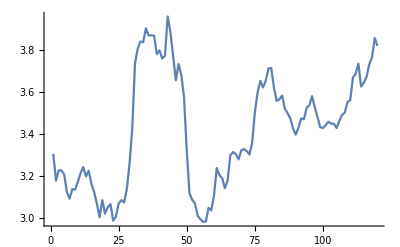

```mathematica
ListLinePlot[milkDataOverTime]
```

### Sugar Price Fluctuation

```mathematica
sugarList=ReadList["Price Data/sugar prices.txt",Number];
```

```mathematica
sugarDataOverTime=Table[{i,sugarList[[i]]},
{i,1,Length[sugarList]}];
```

```mathematica
sugarOT=TimeSeries[sugarDataOverTime];
```

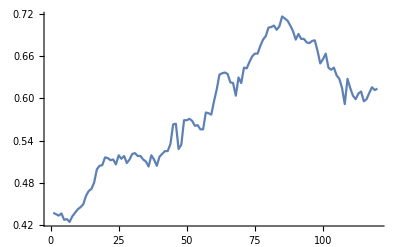

```mathematica
ListLinePlot[sugarOT]
```

### Coffee Prices

```mathematica
(*coffee data by month starting from 2005, January*)
```

```mathematica
coffeeList=ReadList["Price Data/coffee prices.txt",Number];
```

```mathematica
coffeeDataOverTime=Table[{i,coffeeList[[i]]},{i,1,Length[coffeeList]}];
```

```mathematica
coffeeOT=TimeSeries[coffeeDataOverTime];
```

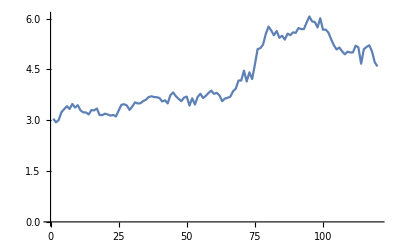

```mathematica
ListLinePlot[coffeeOT]
```

```mathematica
coffeeOT[1] (*jan 2005*)
```

3.049

```mathematica
coffeeOT[13] (*jan 2006*)
```

3.232

### Strawberry Prices

```mathematica
(*strawberry price per 12 ounce from jan 2005-december 2014*)
strawberryList=ReadList["Price Data/strawberry prices.txt",Number];
```

```mathematica
(*convert from 12 ounce to 1 ounce to strawberries per pound.*)
strawberryPerPound=strawberryList/12*16;
```

```mathematica
strawberryDataOverTime=Table[{i,strawberryPerPound[[i]]},{i,1,Length[strawberryPerPound]}];
```

```mathematica
strawberriesOT=TimeSeries[strawberryDataOverTime];
```

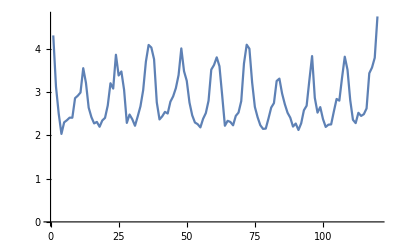

```mathematica
ListLinePlot[strawberriesOT]
```

```mathematica
strawberriesOT[1] (*price per pound jan 2005*)
```

4.312

```mathematica
strawberriesOT[13] (*price per pound jan 2006*)
```

3.21467

```mathematica
strawberriesOT[4] (*price per pound april 2005*)
```

2.03467

### Tea

```mathematica
teaOT[x_]:=6;
```

### Ice

```mathematica
iceOT[x_]:=.85;
```

## Relative Prices Functions

### Prices Relative to Today

```mathematica
(*Function that will accept all the price functions and the current date (date is by month from jan 2005, so 13 is jan 2006) and return a list of graphs for the price of the ingredient over the past month
sInput: price functions, date
Output: graphs for each price over past week*)
uFindPriceBack[priceFunctions_,todaysDate_]:=
Module[{graphList={},i},
For[i=1,i≤Length[priceFunctions],i++,
AppendTo[graphList,Plot[priceFunctions[[i]][t],{t,(todaysDate-1),todaysDate}]];
]; (*interval of one month milk, sugar, coffee*)
Return[graphList]
]
```

```mathematica
functions={milkOT,sugarOT,coffeeOT,teaOT,iceOT,strawberriesOT};
```

```mathematica
(*Function that will accept all the price functions and the current date (date is by month from jan 2005, so 13 is jan 2006) and return a list of graphs for the price of the ingredient over the past month
sInput: price functions, price tea, (constant), price ice (constant),date
Output: graphs for each price over past week*)
uFindPriceNow[priceFunctions_,todaysDate_]:=
Module[{prices={},i},
For[i=1,i≤Length[priceFunctions],i++,
AppendTo[prices,priceFunctions[[i]][todaysDate]];
];
Return[Round[prices,0.01]]
]
```

```mathematica
(*takes the bulk prices of each item and returns the corresponding unit price*)
uFindUnitPrice[ingredientPrices_]:=
Module[{new,conversions},
conversions={16,120,75,40,7,3};
new=ingredientPrices/conversions ;
Return[new]
]
```

## Money Calculation Functions

### Starting Money

```mathematica
(*Determines the starting money the user gets based on the number of days they choose to play*)
uStartingMoney[numOfDays_]:=
Module[{locNum},
(*determine which money to use based on location*)
If[SameQ[location,frankfortList],
(*then*)
locNum=1,
(*else*)
If[SameQ[location,frankfortList],
(*then*)
locNum=2,
(*else*)
locNum=3
]
];

(*determine money based on number of days*)
If[numOfDays≤1,Return[moneyLocationList[[locNum,1]]], (*one day*)
If[numOfDays≤7&&numOfDays≥1,Return[moneyLocationList[[locNum,2]]], (*one week*)
If[numOfDays≤14&&numOfDays≥7, Return[moneyLocationList[[locNum,3]]], (*two weeks*)
Return[moneyLocationList[[locNum,4]]] (*one month*)
];
];
];
]
```

### Price Per Cup

```mathematica
(*these functions take all the recipies and unit prices and calculate how much one making one cup will cost the user*)
uPricePerCupCoffee[currentMoney_,unitPricesPerItem_,milkSugarCoffee_]:=Round[(milkSugarCoffee[[1]]*unitPricesPerItem[[2]])+(milkSugarCoffee[[2]]*unitPricesPerItem[[1]])+(milkSugarCoffee[[3]]*unitPricesPerItem[[3]]),0.01];
```

```mathematica
uPricePerCupTea[currentMoney_,unitPricesPerItem_,teaBags_]:=
Round[(teaBags*unitPricesPerItem[[4]])];
```

```mathematica
uPricePerCupSmoothie[currentMoney_,unitPricesPerItem_,iceStrawberries_]:=
Round[(iceStrawberries[[1]]*unitPricesPerItem[[5]])+(iceStrawberries[[2]]+unitPricesPerItem[[6]])];
```

## Inventory Calculations

### User Needs At Least

```mathematica
(*This function will take in the number of ingredients in each cup of coffee, tea, and smoothie respectively. It will also take in a list of the number of cups of each recipe. It will return the amount of ingredients the user has to have in the order: {gallons of milk, pound of sugar, pound of coffee, green teabag packs, pounds of ice, pounds of strawberries)}.
This is the amount of each item the user needs in their inventory to make it through the day.*)
```

```mathematica
needAtLeast[milkSugarCoffee_,teaBags_,iceStrawberries_,numCoffee_,numTea_,numSmoothie_]:=
Module[{toGallonMilk,toPoundSugar,toPoundCoffee,boxTeaBags,toPoundIce,toPoundStrawberries},
toGallonMilk=Ceiling[(milkSugarCoffee[[1]]*numCoffee)/16]; (*needed gallons of milk*)
toPoundSugar=Ceiling[(milkSugarCoffee[[2]]*numCoffee)/120]; (*needed pounds of sugar (teaspoons)*)
toPoundCoffee=Ceiling[(milkSugarCoffee[[3]]*numCoffee)/75]; (*75 tbs in one pound of coffee*)
boxTeaBags=Ceiling[(teaBags*numTea)/40]; (*40 teabags in one box*)
toPoundStrawberries=Ceiling[(iceStrawberries[[2]]*numSmoothie)/3];(*one pound of strawberries is about 3 cups sliced*)
toPoundIce=Ceiling[(iceStrawberries[[1]]*numSmoothie)/30]; (*one bag has 30 cups of ice*)
Return[{toGallonMilk,toPoundSugar,toPoundCoffee,boxTeaBags,toPoundIce,toPoundStrawberries}]
]
```

### User Has Left

```mathematica
(*This is a function that will subtract from the user's current inventory the ingredients they used throughout the day they used to sell. Any of the remaining items in the inventory will carry over.
Input: user's current inventory, milkSugarCoffee,teaBags,iceStrawberries
Output: The inventory the user has left.*)
```

```mathematica
userHasLeft[userHas_,milkSugarCoffee_,teaBags_,iceStrawberries_,customers_]:=
Module[{userSells={},canMake,i,completeSold,units,coffeeI,teaI,smoothieI,ingredients,bulkUsed,left},
canMake=todayUserCanMake[milkSugarCoffee,teaBags,iceStrawberries,userHas]; (*what user can possibly make*)
completeSold=Table[Total[customers[[i]]],{i,1,Length[customers]}]; (*number bought for each item*)
For[i=1,i≤Length[completeSold],i++,
If[canMake[[i]]>completeSold[[i]],
AppendTo[userSells,completeSold[[i]]];,
AppendTo[userSells,canMake[[i]]];
];
];
units={16,120,75,40,3,30}; (*everything needed to convert from bulk to unit accordingly*)
coffeeI=userSells[[1]]*milkSugarCoffee; (*how many of each ingredient they user by product*)
teaI=userSells[[2]]*teaBags;
smoothieI=userSells[[3]]*iceStrawberries;
ingredients=Flatten[{coffeeI,teaI,smoothieI}]; (*all the used ingredients in one list*)
bulkUsed=Table[Ceiling[ingredients[[i]]/units[[i]]],{i,1,Length[ingredients]}];
left=userHas-bulkUsed;
Return[left]
]
```

### User Can Make

```mathematica
(*This is a function that will take in the amount of ingredients the user currently has and calculate the maximum number that user can possibly make with it.
Input: Amount in each cup of coffee, tea, and smoothies. Amount of bulk items in user's inventory
Output: The number of cups the user can make of everything with their current inventory in bulk*)
```

```mathematica
todayUserCanMake[milkSugarCoffee_,teaBags_,iceStrawberries_,userHas_]:=
Module[{userUnit,conversions,forCoffee,forSmoothie,possibleC,possibleS,possibleT},
conversions={16,120,75,40,3,30}; (*everything needed to convert from bulk to unit accordingly*)
userUnit=userHas*conversions; (*converted units user has*)
forCoffee=Table[userUnit[[i]],{i,1,3}];
forSmoothie=Table[userUnit[[i]],{i,5,6}];

(*Find possible number of coffee cups the user can make with the set recipe*)
If[MemberQ[milkSugarCoffee,0]||MemberQ[milkSugarCoffee,0.],possibleC=0,possibleC=Min[forCoffee/milkSugarCoffee]]; 

(*Find possible number of smoothies the user can make with the set recipe*)
If[MemberQ[iceStrawberries,0]||MemberQ[iceStrawberries,0.],possibleS=0,possibleS=Min[forSmoothie/iceStrawberries]];

(*Find possible number of cups of tea the user can make with the set recipe*)
If[teaBags==0||teaBags==0.,possibleT=0,possibleT=userUnit[[4]]/teaBags];
Return[N[{possibleC,possibleT,possibleS}]//Floor]
]
```

## Tea Customer Calculations

### Basic Daily Amount

```mathematica
(*this function returns the number of customers who will buy tea when nothing is taken into effect*)
customersDailyTea[population_,numberOfStores_ ]:=
Module[{visitors},
visitors=((population)(.0269))/numberOfStores;
Return[Floor[visitors]]
]
```

### Weather Affects on Tea Customers

```mathematica
(*this function returns the percentage affect of tea customers based on a given weather condition*)
weatherConstantTea[condition_]:=
Switch[condition,"Rainy",Return[0.927],"Cloudy",Return[1],"Sunny",Return[0.543],"Humid",Return[0.457],"Snowy",Return[1.099]]
```

```mathematica
(*this fucntion returns the affect a weather condition has on customers*)
weatherCustomersTea[initialTeaCustomers_,weather_]:=
Module[{customers},
customers=weatherConstantTea[weather]*initialTeaCustomers;
Return[customers]
]
```

### Price Affecting Tea Customers

```mathematica
(*when passed price and cusotmers this function returns the number of people who will buy tea at that price*)
uChangePriceTea[q_,customers_]:=N[customers*q^(-1/2)];
```

### Tea Recipe Affect on Customers

```mathematica
(*when passed the number of customers intially and the recipe for tea this function returns how many customers will buy tea with that recipe*)
teaRecipeCustomers[initialTeaCustomers_,teaBags_]:=
Module[{customers},
(*adjust customers based on amount of milk*)
If[teaBags<2,
(*then*)
customers=initialTeaCustomers(.874),
(*else*)
customers=initialTeaCustomers(.985),
(*if equal to 2*)
customers=initialTeaCustomers(1.081)
];
(*Return effect on customers*)
Return[customers//Floor]
]
```

### Tea Customers with all Aspects

```mathematica
(*this function returns the overall effected customers from the aspects which affect tea individually*)
teaCustomersAll[population_, numberOfStores_,teaBags_,price_,conditionList_]:=
Module[{customerList={},initialTeaCustomers,finalTeaCustomers},
(*Calculate initial customers*)
initialTeaCustomers=customersDailyTea[population,numberOfStores];
(*calculate weather affected customers*)
AppendTo[customerList,weatherCustomersTea[initialTeaCustomers, conditionList]];
(*Calculate the recipe's affect on customers*)
AppendTo[customerList,teaRecipeCustomers[initialTeaCustomers,teaBags]];
(*calculate the price's effect*)
AppendTo[customerList,uChangePriceTea[price,initialTeaCustomers]];
(*calculate number of customers with aspects in mind by using a basic average*)
finalTeaCustomers=Mean[customerList]//Floor;
Return[finalTeaCustomers]
]
```

## Coffee Customer Calculations

### Basic Daily Amount

```mathematica
(*this function returns the number of coffee customers who will visit without any effects*)
customersDailyCoffee[demographicsList_,coffeeConsumerData_,numberOfStores_ ]:=
Module[{totalDrinkers,drinkerList,visitorsList},
drinkerList=demographicsList*coffeeConsumerData; (*coffee drinkers*)
visitorsList=drinkerList/numberOfStores; (*one store out of every store in city*)
totalDrinkers=Total[visitorsList];
totalDrinkers=totalDrinkers*.25; (*75% of drinkers drink at home instead of at a coffee shop*)
Return[Floor[totalDrinkers]]
]
```

### Weather Affects on Coffee Customers

```mathematica
(*this function returns the percentage of customers who will come during a certain weather condition*)
weatherConstantCoffee[condition_]:=
Switch[condition,"Rainy",Return[0.936],"Cloudy",Return[1.20],"Sunny",Return[0.746],"Humid",Return[0.694],"Snowy",Return[1.1]]
```

```mathematica
(*this function returns the number of customers after the given weather condition is take into account*)
weatherCustomersCoffee[initialCoffeeCustomers_,weather_]:=
Module[{customers},
customers=weatherConstantCoffee[weather]*initialCoffeeCustomers;
Return[customers]
]
```

### Price Affecting Coffee Customers

```mathematica
(*when given price and initial customers this function returns how many customers will buy coffee at that price*)
uChangePriceCoffee[q_,customers_]:=N[customers*q^(-1/4)];
```

### Coffee Recipe Affecting Customers

```mathematica
(*this function takes in the user's recipe, milkSugarCoffee, and returns the overall recipe effect on number of coffee customers*)
coffeeRecipeCustomers[initialCoffeeCustomers_,milkSugarCoffee_]:=
Module[{customerList={},customers,x},
(*adjust customers based on amount of milk*)
If[milkSugarCoffee[[1]]<2,
(*then*)
AppendTo[customerList,initialCoffeeCustomers(.897)],
(*else*)
AppendTo[customerList,initialCoffeeCustomers(.923)],
(*if equal to 2*)
AppendTo[customerList,initialCoffeeCustomers(1.019)]
];
(*adjust customers based on amount of sugar*)
If[milkSugarCoffee[[2]]<5,
(*then*)
AppendTo[customerList,initialCoffeeCustomers(.967)],
(*else*)
AppendTo[customerList,initialCoffeeCustomers(.801)],
(*if equal to 2*)
AppendTo[customerList,initialCoffeeCustomers(1)]
];

(*adjust customers based on level of coffee beans*)
If[milkSugarCoffee[[3]]<5,
(*then*)
AppendTo[customerList,initialCoffeeCustomers(.888)],
(*else*)
AppendTo[customerList,initialCoffeeCustomers(.945)],
(*if equal to 2*)
AppendTo[customerList,initialCoffeeCustomers(1.112)]
];

(*calculate overall coffee recipe effect*)
customers=Mean[customerList];
Return[customers]
]
```

### Coffee Customers with all Aspects

```mathematica
(*this function accounts for all the aspects which affect coffee customers directly and return the number of customers who will visit and buy coffee when all of these are taken into account*)
coffeeCustomersAll[demographicsList_,coffeeConsumerData_, numberOfStores_,milkSugarCoffee_,price_,conditionList_]:=
Module[{customerList={},initialCoffeeCustomers,finalCoffeeCustomers},
(*Calculate initial customers*)
initialCoffeeCustomers=customersDailyCoffee[demographicsList,coffeeConsumerData,numberOfStores];

(*calculate weather affected customers*)
AppendTo[customerList,weatherCustomersCoffee[initialCoffeeCustomers, conditionList]];
(*Calculate the recipe's affect on customers*)
AppendTo[customerList,coffeeRecipeCustomers[initialCoffeeCustomers,milkSugarCoffee]];
(*calculate the price's effe\ct*)
AppendTo[customerList,uChangePriceCoffee[price,initialCoffeeCustomers]];
(*calculate number of customers with aspects in mind by using a basic average*)
finalCoffeeCustomers=Mean[customerList]//Floor;
Return[finalCoffeeCustomers]
]
```

## Smoothie Customer Calculations

### Basic Daily Amount

```mathematica
(*calculate the intial customers who would come and buy smoothies with no effects accounted for*)
customersDailySmoothie[population_,numberOfStores_ ]:=
Module[{visitors},
visitors=((population)(.0469))/numberOfStores;
Return[Floor[visitors]]
]
```

### Weather Affects on Smoothie Customers

```mathematica
(*this function returns the percentage of customes which will still buy smoothies during a certain weather condition*)
weatherConstantSmoothie[condition_]:=
Switch[condition,"Rainy",Return[0.657],"Cloudy",Return[0.96],"Sunny",Return[1.35],"Humid",Return[1.288],"Snowy",Return[.32]]
```

```mathematica
(*the function accounts for the weather by returning the intial customers multiplies by the appropriate weather constant*)
weatherCustomersSmoothie[initialSmoothieCustomers_,weather_]:=
Module[{customers},
customers=weatherConstantSmoothie[weather]*initialSmoothieCustomers;
Return[customers]
]
```

### Price Affecting Smoothie Customers

```mathematica
(*when given the price (q) and customera this returns the number of customers who will come when a smoothie is that price*)
uChangePriceSmoothie[q_,customers_]:=N[customers*q^(-3/4)];
```

### Smoothie Recipe Affect on Customers

```mathematica
(*this function takes in the user's recipe for their smoothie and returns the overall recipe effect on smoothie customers*)
smoothieRecipeCustomers[initialSmoothieCustomers_,iceStrawberries_]:=
Module[{customerList={},customers},
(*adjust customers based on ice*)
If[iceStrawberries[[1]]<2,
(*then*)
AppendTo[customerList,initialSmoothieCustomers(1)],
(*else*)
AppendTo[customerList,initialSmoothieCustomers(.874)],
(*if equal to 2*)
AppendTo[customerList,initialSmoothieCustomers(1.201)]
];
(*adjust customers based on strawberries*)
If[iceStrawberries[[2]]<1.5,
(*then*)
AppendTo[customerList,initialSmoothieCustomers(.807)],
(*else*)
AppendTo[customerList,initialSmoothieCustomers(1.342)],
(*if equal to 2*)
AppendTo[customerList,initialSmoothieCustomers(1)]
];
(*calculate overall effect*)
customers=Mean[customerList];
Return[customers//Floor]
]
```

### Smoothie Customers Accounting for All Aspects

```mathematica
(*this function accounts for all the aspects which affect smoothie customers directly and return the number of customers who will visit when all of these are taken into account*)
smoothieCustomersAll[population_, numberOfStores_,iceStrawberries_,price_,conditionList_]:=
Module[{customerList={},initialSmoothieCustomers,finalSmoothieCustomers},
(*Calculate initial customers*)
initialSmoothieCustomers=customersDailySmoothie[population,numberOfStores];
(*calculate weather affected customers*)
AppendTo[customerList,weatherCustomersSmoothie[initialSmoothieCustomers, conditionList]];
(*Calculate the recipe's affect on customers*)
AppendTo[customerList,smoothieRecipeCustomers[initialSmoothieCustomers,iceStrawberries]];
(*calculate the price's effect*)
AppendTo[customerList,uChangePriceSmoothie[price,initialSmoothieCustomers]];
(*calculate number of customers with aspects in mind by using a basic average*)
finalSmoothieCustomers=Mean[customerList]//Floor;
Return[finalSmoothieCustomers]
]
```

## Overall Customers

### WiFi Affecting Customers

```mathematica
(*when given a list of customers and whether or not the store has wifi return the list of customers with the effect from wifi*)
wifiCustomers[wifiBoolean_,customersList_]:=
Module[{},
If[wifiBoolean,
(*then*)
Return[Floor[customersList*1.134]],
(*else*)
Return[customersList]
]
]
```

### Store Layout Affecting Customers

```mathematica
(*Based on the layout of the store return the number of customers affected store layout has been accounted for*)
storeLayoutCustomers[storeLayout_,customersList_]:=
Module[{},
If[storeLayout==storeLayoutsList[[1]],
(*then*)
Return[customersList(.875)],
(*else*)
If[storeLayout==storeLayoutsList[[2]],
(*then*)
Return[customersList],
(*else*)
Return[customersList(1.325)]
]
]
]
```

### Advertisements Affecting Customers

```mathematica
(*account for the effect adds have on the number of customers and return the affected list*)
adsCustomers[advertisementsList_,customersList_]:=
Module[{adsCustomersList={}},
(*check if there are ads*)
If[!SameQ[Position[advertisementsList,0],{}],
(*then*)
Return[customersList(.681)]
];
(*in the prescence of ads calculate ads effect on customers*)
(*check for flyers*)
If[!SameQ[Position[advertisementsList,1],{}],
(*then*)
AppendTo[adsCustomersList,customersList(.858)]
];
(*check for website*)
If[!SameQ[Position[advertisementsList,2],{}],
(*then*)
AppendTo[adsCustomersList,customersList(.962)]
];
(*check for commercials*)
If[!SameQ[Position[advertisementsList,3],{}],
(*then*)
AppendTo[adsCustomersList,customersList(1.437)]
];
(*Return average of all the customer affected list*)
Return[Mean[adsCustomersList]]
]
```

### Employees and Location Affecting Customers

```mathematica
(*this functions takes in an initial value of customers, the number of employees, and the location and determines the affected number of customers based on how many employees you've hired in your location*)
employeeLocationCustomers[customers_,numOfEmployees_,location_]:=
Module[{frankfortOptions={2,3,4,5},tallahasseeOptions={2,4,6,8},losAngelesOptions={2,5,8,10},options},
(*determine options based on location*)
options=Switch[location,frankfortList,frankfortOptions,losAngelesList,losAngelesOptions,tallahasseeList,tallahasseeOptions];

(*return number customers based on how many employees you have*)
Switch[numOfEmployees,
options[[1]],Return[customers(.875)],
options[[2]],Return[customers(.937)],
options[[3]],Return[customers(1.102)],
options[[4]],Return[customers(1.237)]
]
]
```

### Total Customers Visiting

```mathematica
(*calculate the total daily amount of customers with everything in consideration*)
totalDailyCustomers[population_,demographicsList_,coffeeConsumerData_,numberOfStores_,milkSugarCoffee_,iceStrawberries_,teaBags_, userPrices_,weather_,wifiBoolean_,storeLayout_,advertisementsList_]:=
Module[{finalCustomersList={},customersList,smoothieCustomers,coffeeCustomers, teaCustomers},

(*calculate smoothie customers before overall effects*)
smoothieCustomers=smoothieCustomersAll[population, numberOfStores,iceStrawberries,userPrices[[3]], weather];

(*calculate coffee customers before overall effects*)
coffeeCustomers=coffeeCustomersAll[demographicsList,coffeeConsumerData, numberOfStores, milkSugarCoffee,userPrices[[1]], weather];

(*calculate tea customers before overall effects*)
teaCustomers=teaCustomersAll[population, numberOfStores, teaBags, userPrices[[2]], weather];

(*define customers list to use*)
customersList={coffeeCustomers,teaCustomers,smoothieCustomers};

(*calculate wifi affect on customers*)
AppendTo[finalCustomersList,wifiCustomers[wifiBoolean,customersList]];

(*calculate store layout affect on customers*)
AppendTo[finalCustomersList,storeLayoutCustomers[storeLayout,customersList]];

(*calculate the effect from advertisments*)
AppendTo[finalCustomersList,adsCustomers[advertisementsList,customersList]];

(*calculate the effect from number of employees*)
AppendTo[finalCustomersList,employeeLocationCustomers[customersList,numOfEmployees,location]];

(*average the overall effects on customers*)
finalCustomersList=Mean[finalCustomersList];

(*multiply the final list by the cusotmer satisfaction ratios*)
finalCustomersList=finalCustomersList*cSat;

(*return a list of the final coffee, tea, and smoothie customers*)
Return[finalCustomersList//Floor]
]
```

## Location Effect Functions

### Suggested Cups

```mathematica
(*this function returns the right list of suggested cup making values based on location*)
suggestedList[loc_]:=
Switch[loc,
frankfortList,frankfortSuggest,
losAngelesList,laSuggest,
tallahasseeList,tallahasseeSuggest
]
```

## Data Generating Functions

### Coffee Cups Sold Hourly

```mathematica
(*this function generates a list of hourly data for the customers who will come to the store and get coffee each hour*)
coffeeCupsSoldHourly[coffeeC_]:=
Module[{hold,r,cList={},cCo},
(*7-10*)
hold=
Table[
r=RandomInteger[{10,Ceiling[coffeeC/7]}];
r
,{3}];
AppendTo[cList,hold];

(*10-12*)
hold=
Table[
r=RandomInteger[{1,Ceiling[coffeeC/14]}];
r
,{2}];
AppendTo[cList,hold];

(*12-2*)
hold=
Table[
r=RandomInteger[{10,Ceiling[coffeeC/7]}];
r
,{2}];
AppendTo[cList,hold];

(*2-5*)
hold=
Table[
r=RandomInteger[{1,Ceiling[coffeeC/20]}];
r
,{3}];
AppendTo[cList,hold];

(*5-9*)
hold=
Table[
r=RandomInteger[{5,Ceiling[coffeeC/14]}];
r
,{4}];
AppendTo[cList,hold];

(*Generate hourly list*)
cList=Flatten[cList];

(*Generate list coefficient*)
cCo=coffeeC/Total[cList];

(*Apply coefficient to list to raise total*)
cList=cList*cCo;

(*Randomly round the numbers up or down to an integer because you can't sell a fraction of a cup*)
If[RandomInteger[]==1,
(*then*)
cList=cList//Floor;,
(*else*)
cList=cList//Ceiling;
];
Return[cList]
]
```

### Tea Cups Sold Hourly

```mathematica
(*this function generates a list of hourly data for the customers who will come to the store and get tea each hour when given the customers for the day*)
teaCupsSoldHourly[teaC_]:=
Module[{hold,r,tList={},tCo},
(*7-10*)
hold=
Table[
r=RandomInteger[{10,Ceiling[teaC/7]}];
r
,{3}];
AppendTo[tList,hold];

(*10-12*)
hold=
Table[
r=RandomInteger[{1,Ceiling[teaC/14]}];
r
,{2}];
AppendTo[tList,hold];

(*12-2*)
hold=
Table[
r=RandomInteger[{10,Ceiling[teaC/7]}];
r
,{2}];
AppendTo[tList,hold];

(*2-5*)
hold=
Table[
r=RandomInteger[{1,Ceiling[teaC/20]}];
r
,{3}];
AppendTo[tList,hold];

(*5-9*)
hold=
Table[
r=RandomInteger[{5,Ceiling[teaC/14]}];
r
,{4}];
AppendTo[tList,hold];

(*Generate hourly list*)
tList=Flatten[tList];

(*Generate list coefficient*)
tCo=teaC/Total[tList];

(*Apply coefficient to list to raise total*)
tList=tList*tCo;

(*Randomly round the numbers up or down to an integer because you can't sell a fraction of a cup*)
If[RandomInteger[]==1,
(*then*)
tList=tList//Floor;,
(*else*)
tList=tList//Ceiling;
];
Return[tList]
]
```

### Smoothie Cups Sold Hourly

```mathematica
(*this function generates a list of hourly data for the customers who will come to the store and get a smoothie each hour*)
smoothieCupsSoldHourly[smoothieC_]:=
Module[{hold,r,sList={},sCo},
(*7-10*)
hold=
Table[
r=RandomInteger[{10,Ceiling[smoothieC/7]}];
r
,{3}];
AppendTo[sList,hold];

(*10-12*)
hold=
Table[
r=RandomInteger[{1,Ceiling[smoothieC/14]}];
r
,{2}];
AppendTo[sList,hold];

(*12-2*)
hold=
Table[
r=RandomInteger[{10,Ceiling[smoothieC/7]}];
r
,{2}];
AppendTo[sList,hold];

(*2-5*)
hold=
Table[
r=RandomInteger[{1,Ceiling[smoothieC/20]}];
r
,{3}];
AppendTo[sList,hold];

(*5-9*)
hold=
Table[
r=RandomInteger[{5,Ceiling[smoothieC/14]}];
r
,{4}];
AppendTo[sList,hold];

(*Generate hourly list*)
sList=Flatten[sList];

(*Generate list coefficient*)
sCo=smoothieC/Total[sList];
(*Apply coefficient to list to raise total*)
sList=sList*sCo;

(*Randomly round the numbers up or down to an integer because you can't sell a fraction of a cup*)
If[RandomInteger[]==1,
(*then*)
sList=sList//Floor;,
(*else*)
sList=sList//Ceiling;
];
Return[sList]
]
```

### Overall

```mathematica
(*this function calculates the hourly data for customers who come to the store and buy each product and returns that list*)
cupsSoldHourly[]:=
Module[{coffeeC,teaC,smoothieC,cList,tList,sList,customersList,actualMade},
(*calculate cusotmers*)
customersList=totalDailyCustomers[population,agePops,drinkingPerentages,numberOfStores,milkSugarCoffee,iceStrawberries,teaBags,userPrices,weather,wifiBoolean,storeLayout,adList];
coffeeC=customersList[[1]];
teaC=customersList[[2]];
smoothieC=customersList[[3]];
(*Generate hourly data for products with distribution*)
cList=coffeeCupsSoldHourly[coffeeC];
tList=teaCupsSoldHourly[teaC];
sList=smoothieCupsSoldHourly[smoothieC];

(*Return list of all the hourly data*)
Return[{cList,tList,sList}]
]
```

### Data Checking Function

```mathematica
(*this function remakes the hourly data list based on how many cups of each product the user can actually make*)
hourlyDataCheck[]:=
Module[{cupsC=Total[coffeeCupsHourly],cupsT=Total[teaCupsHourly],cupsS=Total[smoothieCupsHourly],i,hold=0,holdLst={},iHold,pHold,j,actualMade,cCupsMade,tCupsMade,sCupsMade},

(*Find the actual number of cups the user will make based on their inventory*)
actualMade=todayUserCanMake[milkSugarCoffee,teaBags,iceStrawberries,userHas];
cCupsMade=actualMade[[1]];
tCupsMade=actualMade[[2]];
sCupsMade=actualMade[[3]];

(*Check coffee data and make it account for running out of cups*)
If[cCupsMade<cupsC,
If[cCupsMade==0,
(*then*)
coffeeCupsHourly=Table[0,{Length[coffeeCupsHourly]}],
(*else*)
hold=0;
For[i=1,i≤Length[coffeeCupsHourly],i++,
hold+=coffeeCupsHourly[[i]];
AppendTo[holdLst,hold];
If[hold>cCupsMade,
iHold=Length[coffeeCupsHourly]-i;
If[i==1,
(*then*)
pHold=cCupsMade,
(*else*)
pHold=cCupsMade-holdLst[[Length[holdLst]-1]]
];
coffeeCupsHourly=Insert[coffeeCupsHourly,pHold,-1(iHold+1)];
coffeeCupsHourly=Delete[coffeeCupsHourly,-1(iHold+2)];
coffeeCupsHourly=Take[coffeeCupsHourly,Length[coffeeCupsHourly]-iHold];
For[j=1,j≤iHold,j++,
AppendTo[coffeeCupsHourly,0]
];
i=Length[coffeeCupsHourly]+1;
]
]
]
];

(*reset holdLst*)
holdLst={};

(*Check tea data and make it account for running out of cups*)
If[tCupsMade<cupsT,
If[tCupsMade==0,
(*then*)
teaCupsHourly=Table[0,{Length[teaCupsHourly]}],
(*else*)
hold=0;
For[i=1,i≤Length[teaCupsHourly],i++,
hold+=teaCupsHourly[[i]];
AppendTo[holdLst,hold];
If[hold>tCupsMade,
iHold=Length[teaCupsHourly]-i;
If[i==1,
(*then*)
pHold=tCupsMade,
(*else*)
pHold=tCupsMade-holdLst[[Length[holdLst]-1]]
];
teaCupsHourly=Insert[teaCupsHourly,pHold,-1(iHold+1)];
teaCupsHourly=Delete[teaCupsHourly,-1(iHold+2)];
teaCupsHourly=Take[teaCupsHourly,Length[teaCupsHourly]-iHold];
For[j=1,j≤iHold,j++,
AppendTo[teaCupsHourly,0]
];
i=Length[teaCupsHourly]+1;
]
]
]
];

(*reset holdLst*)
holdLst={};

(*Check smoothie data and make it account for running out of cups*)
If[sCupsMade<cupsS,
If[sCupsMade==0,
(*then*)
smoothieCupsHourly=Table[0,{Length[smoothieCupsHourly]}],
(*else*)
hold=0;
For[i=1,i≤Length[smoothieCupsHourly],i++,
hold+=smoothieCupsHourly[[i]];
AppendTo[holdLst,hold];
If[hold>sCupsMade,
iHold=Length[smoothieCupsHourly]-i;
If[i==1,
(*then*)
pHold=sCupsMade,
(*else*)
pHold=sCupsMade-holdLst[[Length[holdLst]-1]]
];
smoothieCupsHourly=Insert[smoothieCupsHourly,pHold,-1(iHold+1)];
smoothieCupsHourly=Delete[smoothieCupsHourly,-1(iHold+2)];
smoothieCupsHourly=Take[smoothieCupsHourly,Length[smoothieCupsHourly]-iHold];
For[j=1,j≤iHold,j++,
AppendTo[smoothieCupsHourly,0]
];
i=Length[smoothieCupsHourly]+1;
]
]
]
]
]
```

### Calculate Data Function

```mathematica
(*Calculates data based on the predicted approximate number of customers that will visit the store or how many cups you can actually make*)
calculateProductData[]:=
Module[{cupsToday},
cupsToday=cupsSoldHourly[];
(*calculate hourly data*)
coffeeCupsHourly=cupsToday[[1]];
teaCupsHourly=cupsToday[[2]];
smoothieCupsHourly=cupsToday[[3]];
(*append to the list of customers who visited in the day for each product*)
customersWhoDidVisit={};
AppendTo[customersWhoDidVisit,Total[coffeeCupsHourly]];
AppendTo[customersWhoDidVisit,Total[teaCupsHourly]];
AppendTo[customersWhoDidVisit,Total[smoothieCupsHourly]];
(*check and update for customer satisfaction*)
cSatCheck[];
(*fix data to fit the day*)
hourlyDataCheck[];
(*Calculate overall data for throughout the simulation*)
AppendTo[coffeeCupsData,Total[coffeeCupsHourly]];
AppendTo[teaCupsData,Total[teaCupsHourly]];
AppendTo[smoothieCupsData,Total[smoothieCupsHourly]];
]
```

## Store Layout Count Functions

### Count Determining Function

```mathematica
(*this function set the storeLayoutCount back to one if the current layout isn't the same as the previous layout*)
updateStoreLayoutCount[]:=
Module[{},
If[currentDay==1,
(*then*)
storeLayoutCount=1,
(*else*)
If[!SameQ[layoutsList[[1]],layoutsList[[2]]],
(*then*)
storeLayoutCount=1,
(*else*)
storeLayoutCount++;
];
]
]
```

### List Changing Function

```mathematica
(*this function sets the layoutList to the new previous layout and current layout*)
updateLayoutList[]:=
DynamicModule[{lst=layoutsList},
layoutsList={lst[[2]],storeLayout};
]
```

## Expenses Decrement Function

### Advertisements Decrement

```mathematica
advertisementDecrement[]:=
Module[{deduction=0},

(*If there are no ads deduct no money*)
If[!SameQ[Position[adList,0],{}],
(*then*)
Return[0];
];

(*check for flyers and add the deduction to the advertisement deduction*)
If[!SameQ[Position[adList,1],{}],
(*then*)
deduction+=adCosts[[1]];
];

(*check for website and add the deduction to the advertisement deduction*)
If[!SameQ[Position[adList,2],{}],
(*then*)
deduction+=adCosts[[2]];
];

(*check for commercials and add the deduction to the advertisement deduction*)
If[!SameQ[Position[adList,3],{}],
(*then*)
deduction+=adCosts[[3]];
];

(*Return the deduction*)
Return[deduction]
]
```

### Store Payment Fucntion

```mathematica
(*this function returns the correct store layout cost based on the store layout, count, and location*)
storePayment[storeLayout_,slc_,loc_]:=
Module[{list},
(*determine whihc prices to use by layout*)
Switch[storeLayout,
storeLayoutsList[[1]],list={{150,0},{200,20},{450,50}},
storeLayoutsList[[2]],list={{275,50},{400,80},{650,100}},
storeLayoutsList[[3]],list={{400,80},{750,125},{1000,250}}
];
(*determine which of the price set to use based on location*)
Switch[loc,
frankfortList,list=list[[1]],
tallahasseeList,list=list[[2]],
losAngelesList,list=list[[3]]
];
(*determoine which price to use based on the storeLayoutCount*)
If[slc==1,
list=list[[1]],
list=list[[2]]
];
Return[list]
]
```

### Overall Expense Function

```mathematica
(*this function takes away your expenses form you money and adds the total expense for the day into the list of expenses for the calculation*)
expensesDecrement[]:=
Module[{sDeduction,aDeduction,eDeduction,wDeduction,mDeduction,totalDeduction},
(*Subtract employee cost assuming minimum wage and employees working 13 hours in a day*)
eDeduction=numOfEmployees(13)(7.25);
currentMoney-=eDeduction;

(*Subtract cost of wifi if your store has wifi*)
If[wifiBoolean,
(*then*)
wDeduction=wifiCost;
currentMoney-=wifiCost,
(*else*)
wDeduction=0;
];

(*Subtract cost of store layout*)
sDeduction=storePayment[storeLayout,storeLayoutCount,location];
currentMoney-=sDeduction;

(*the the deduction from advertisements*)
aDeduction=advertisementDecrement[];
currentMoney-=aDeduction;

(*deduct materials cost*)
mDeduction=Round[.35(Total[Total[customers]]),.01];
currentMoney-=mDeduction;

(*add total deduction and append it to the list*)
totalDeduction=wDeduction+sDeduction+eDeduction+aDeduction+mDeduction;
individualExpenses={wDeduction,sDeduction,eDeduction,aDeduction,mDeduction};
AppendTo[totalExpenses,totalDeduction];
]
```

## Money and Profit Functions

### Money Made Function

```mathematica
(*this function calculates the money made the user makes from everthing they sold (not deducting expenses)*)
uMakeMoney[userPrices_]:=Module[{cups,hours,hoursMoney,cupsMoney},
cups=customers;
cupsMoney=cups*userPrices;
hours=Table[cupsMoney[[All,i]],{i,1,Length[cupsMoney[[1]]]}]; (*corresponding money made every hour*)
hoursMoney=Table[Total[hours[[i]]],{i,1,Length[hours]}]; (*total money made every hour*)
Return[Round[hoursMoney,0.01]]
]
```

### Profit Function

```mathematica
(*function to calculate the profit by adding all the money made from the selling of products and subtracting the day's expenses*)
calculateProfit[]:=
Module[{coffeeP,teaP, smoothieP,profit},
coffeeP=userPrices[[1]](coffeeCupsHourly);
teaP=userPrices[[2]](teaCupsHourly);
smoothieP=userPrices[[3]](smoothieCupsHourly);
profit=Total[coffeeP]+Total[teaP]+Total[smoothieP]-totalExpenses[[currentDay]];
AppendTo[totalProfit,profit];
]
```

### Current Money Tracker Function

```mathematica
addMoneyData[]:=
AppendTo[currentMoneyList,currentMoney]
```

## Spoiling Functions

### Spoiling Constant Function

```mathematica
(*Return the proper number of days for the given ingredient before it spoils*)
spoilingConstant[x_]:=Switch[x,1,Return[7],2,Return[-1],3,Return[185],4,Return[240],5,Return[-1],6,Return[5]]
```

### Decrement Spoiling Function

```mathematica
(*function to decrement each constant in the spoiling list which keeps track of the days ingredients have until they spoil*)
decrementSpoiling[]:=
Module[{i,j},
For[i=1,i≤6,i++,
For[j=1,j≤ Length[spoilingList[[i]]],j++,
spoilingList[[i,j]]-=1;
]
]
]
```

### Check and Remove Spoiled Ingredients Function

```mathematica
(*function to check for spoiled ingredients and delete them from the inventory if they spoiled*)
checkAndRemoveSpoiled[]:=
Module[{i,j,posOfZeros,listSpoiled={},length1,length2},
spoiledList={{},{},{},{},{},{}};
For[i=1,i≤6,i++,
If[!SameQ[Position[spoilingList[[i]],0],{}],
(*then find the zeros delete them and save how many there were*)
length1=Length[spoilingList[[i]]];(*find length of list before removing spoiled*)
posOfZeros=Position[spoilingList[[i]],0];
spoilingList[[i]]=Delete[spoilingList[[i]],posOfZeros];
length2=Length[spoilingList[[i]]];(*find length after 0's are deleted*)
AppendTo[listSpoiled,Length[posOfZeros]];
AppendTo[spoiledList[[i]],length1-length2],
(*else append to the lists 0 for no spoiled ingredients*)
AppendTo[listSpoiled,0];
AppendTo[spoiledList[[i]],0];
];
(*Delete from the spoiled list negative numbers after they've been decremented because the ingredient won't spoil this way they don't clog up the list*)
spoilingList[[i]]=Delete[spoilingList[[i]],Position[spoilingList[[i]],-2]];
];
For[i=1,i≤6,i++,
userHas[[i]]-=listSpoiled[[i]]
];
]
```

### Function to Remove Used Ingredient Spoiling Constants

```mathematica
(*function to removed the spoiling constants of ingredients as they get used in a day*)
removeUsedSpoilingConstants[]:=
Module[{i,hasLeft,userHas=userHas},
hasLeft=userHasLeft[userHas,milkSugarCoffee,teaBags,iceStrawberries,customers];
For[i=1,i≤6,i++,
spoilingList[[i]]=Take[spoilingList[[i]],-1(hasLeft[[i]])]
]
]
```

## Graphics

```mathematica
(*Finds the number of customers to graphically display every day. The customers are represented proportionally by 25 figures, as to avoid crowding*)
uFindCustomerRatio[customersWhoDidVisit_]:=
Module[{total=Total[customersWhoDidVisit],multiply,newList},
If[total==0,
Return[{0,0,0}],
multiply=customersWhoDidVisit/total; (*the ratios*)
];
newList=multiply*25.//Ceiling; (*the total number of each color to display*)
Return[newList]
]
```

```mathematica
(*Finds the number of customers out of 25 who actually bought an item
Input: Total customers visited out of 25, the number of cups sold*)
uFindSoldRatio[ratioList_,userSold_]:=
Module[{percentageSold,items,sell},
items=Table[Total[userSold[[i]]],{i,1,Length[userSold]}];
If[Total[items]==0,
Return[{0,0,0}],
percentageSold=Table[items[[i]]/ratioList[[i]],{i,1,Length[ratioList]}]; (*percent of coffee, tea, smoothie sold out of all visiting customers*)
(*sell=N[ratioList*percentageSold]//Ceiling;*)
Return[N[percentageSold]//Ceiling]
];
]
```

```mathematica
(*function that will return a list of disks at the given coordinates.
Input: Customers that visited ratio, the customers that bought something,coordinates for all the disks
Output: A list of disks at the given coordinates, a dollar sign if that item has been bought*)
uMoveAcrossScreen[dailyCustomers_,userSold_,coordinates_]:=
Module[{person,people,colors={Brown,Darker[Green],Lighter[Pink]},i,customers={},count=0,countBought={0,0,0},toSell,dollar},
toSell=uFindSoldRatio[dailyCustomers,userSold]; (*number of customers that will buy something of each ingredient*)
For[i=1,i≤Length[dailyCustomers],i++,
people=Table[
Graphics[{
colors[[i]], (*right color*)
Disk[coordinates[[j+count]],6],
If[coordinates[[j+count,1]]≥50&&toSell[[i]]≥countBought[[i]]&&toSell[[i]]≠0, (*if the disk has traveled half the screen and there is more to be sold*)
dollar=Text["$$$",coordinates[[j+count]]];
countBought[[i]]++;, (*increments the number sold*)
dollar=Text[""];
];
Black,
Style[dollar,Large,Bold],
Darker[Brown],
Rectangle[{-3.5,-10},{9.5,10}],
Black,
Disk[{6,1},0.8]
} (*create disk*)
,PlotRange->{{0,100},{-10,10}}]
,{j,1,dailyCustomers[[i]]}
];
count+=dailyCustomers[[i]]; (*make sure disk is at right coordinate*)
AppendTo[customers,people]
];
Return[Flatten[customers]]
]
```

```mathematica
(*run the task to make the disks move across screen*)
moveX[]:=RunScheduledTask[
coordinates[[All,1]]+=.5,
{.03,1500}];
```

```mathematica
(*function that will display the customers moving across the screen graphically
Input: The customer numbers and number actually sold
Output: The customers displayed graphically*)
uShowCustomers[customersWhoDidVisit_,userSold_]:=
DynamicModule[{dailyCustomers},
dailyCustomers=uFindCustomerRatio[customersWhoDidVisit]; (*customers that visit store for each ingredient*)
coordinates=Table[{-(i*15),0},{i,0,Total[dailyCustomers]}]; (*where each customer starts*)
moveX[]; (*moves customers*)
Panel[Dynamic[Show[uMoveAcrossScreen[dailyCustomers,userSold,coordinates],ImageSize->{1000,100}]]]
]
```

## Screens

## Review Screen

### Plots

#### Tooltip Checking Functions

```mathematica
(*Function to return single or plural time unit depending on the value*)
stringCheckerDays[i_]:=
If[i==1,
" day",
" days"]
```

```mathematica
(*Function to return single or plural time unit depending on the value*)
stringCheckerHours[i_]:=
If[i==1,
" hour",
" hours"]
```

```mathematica
(*Function to return the singlular or plural form of "cups" depending on the value*)
stringCheckerCups[i_]:=
If[i==1,
" cup",
" cups"]
```

#### Individual Products Cups Sold Plots

```mathematica
(*Function that returns day review plots when given the hourly data for a single product*)
dayReview[cupsHourly_]:=
Module[{newList,newListP,display},
(*create point list for the line plot*)
newList=
Table[{i,cupsHourly[[i]]},{i,1,Length[cupsHourly]}];
(*create tooltipped list for the listplot*)
newListP=
Table[Tooltip[{i,cupsHourly[[i]]},{ToString[i]<>stringCheckerHours[i]<>", "<>ToString[cupsHourly[[i]]]<>stringCheckerCups[cupsHourly[[i]]]<> " sold"}],{i,1,Length[cupsHourly]}];
(*generate and return the display of the data plot*)
display=
Show[
ListPlot[newListP,PlotRange->All,ImageSize->Full],
ListLinePlot[newList,PlotRange->All,ImageSize->Full]
];
Return[display]
]
```

```mathematica
(*function that returns overall plots for the simulation when given the overall data for one product*)
overallCups[cupsData_]:=
Module[{newList,newListP,display},
(*generate point lists from given data*)
newList=
Table[{i,cupsData[[i]]},{i,1,Length[cupsData]}];
newListP=
Table[Tooltip[{i,cupsData[[i]]},{ToString[i]<>stringCheckerDays[i]<>", "<>ToString[cupsData[[i]]]<>stringCheckerCups[cupsData[[i]]]<>" sold"}],{i,1,Length[cupsData]}];

(*generate display and return it*)
display=
Show[
ListPlot[newListP,PlotRange->All,ImageSize->Full],
ListLinePlot[newList,PlotRange->All,ImageSize->Full]
];
Return[display]
]
```

#### Individual Products Money Made Plots

```mathematica
(*function to return the plot of money made each hour over the course of a day for a single product*)
moneyThroughTheDay[cupsHourly_,price_]:=
Module[{newList,newListP,display},
(*generate point lists from given data*)
newList=
Table[{i,price(cupsHourly[[i]])},{i,1,Length[cupsHourly]}];
newListP=
Table[Tooltip[{i,price(cupsHourly[[i]])},{ToString[i]<>stringCheckerHours[i]<>", "<>ToString[price cupsHourly[[i]]]<>" dollars"}],{i,1,Length[cupsHourly]}];

(*generate display and return it*)
display=
Show[
ListPlot[newListP,PlotRange->All,ImageSize->Full],
ListLinePlot[newList,PlotRange->All,ImageSize->Full]
];
Return[display]
]
```

```mathematica
(*function to plot the money made over the simulation over the course of one day for a single product*)
overallMoneyPlot[cupsData_,price_]:=
Module[{newList,newListP,display},
(*generate point list from given data*)
newList=
Table[{i,price(cupsData[[i]])},{i,1,Length[cupsData]}];
newListP=
Table[Tooltip[{i,price(cupsData[[i]])},{ToString[i]<>stringCheckerDays[i]<>", "<>ToString[price(cupsData[[i]])]<>" dollars"}],{i,1,Length[cupsData]}];

(*generate display and return it*)
display=
Show[
ListPlot[newListP,PlotRange->All,ImageSize->Full],
ListLinePlot[newList,PlotRange->All,ImageSize->Full]
];
Return[display]
]
```

#### Overall Data Plot Function

```mathematica
(*Function to generate overall data for all products and the tota;*)
overallData[coffeeH_,teaH_,smoothieH_,type_]:=
Module[{totalList,listC,listT,listS,display,plotC,plotT,plotS,plotO,listC2,listS2,listT2,totalList2},
(*Generate total lists*)
totalList=coffeeH+teaH+smoothieH;
totalList2=coffeeH+teaH+smoothieH;

If[SameQ["hours",type],
(*then*)
(*Generate tooltipped data points from hourly data lists given*)
totalList=Table[Tooltip[{i,totalList[[i]]},{ToString[i]<>stringCheckerHours[i]<>", "<>ToString[totalList[[i]]]<>stringCheckerCups[totalList[[i]]]<>" sold"}],{i,1,Length[totalList]}];

listC=Table[Tooltip[{i,coffeeH[[i]]},{ToString[i]<>stringCheckerHours[i]<>", "<>ToString[coffeeH[[i]]]<>stringCheckerCups[coffeeH[[i]]]<>" sold"}],{i,1,Length[coffeeH]}];

listT=Table[Tooltip[{i,teaH[[i]]},{ToString[i]<>stringCheckerHours[i]<>", "<>ToString[teaH[[i]]]<>stringCheckerCups[teaH[[i]]]<>" sold"}],{i,1,Length[teaH]}];

listS=Table[Tooltip[{i,smoothieH[[i]]},{ToString[i]<>stringCheckerHours[i]<>", "<>ToString[smoothieH[[i]]]<>stringCheckerCups[smoothieH[[i]]]<>" sold"}],{i,1,Length[smoothieH]}];
,
(*else*)
(*Generate tooltipped data points from overall data lists given*)
totalList=Table[Tooltip[{i,totalList[[i]]},{ToString[i]<>stringCheckerDays[i]<>", "<>ToString[totalList[[i]]]<>stringCheckerCups[totalList[[i]]]<>" sold"}],{i,1,Length[totalList]}];

listC=Table[Tooltip[{i,coffeeH[[i]]},{ToString[i]<>stringCheckerDays[i]<>", "<>ToString[coffeeH[[i]]]<>stringCheckerCups[coffeeH[[i]]]<>" sold"}],{i,1,Length[coffeeH]}];

listT=Table[Tooltip[{i,teaH[[i]]},{ToString[i]<>stringCheckerDays[i]<>", "<>ToString[teaH[[i]]]<>stringCheckerCups[teaH[[i]]]<>" sold"}],{i,1,Length[teaH]}];

listS=Table[Tooltip[{i,smoothieH[[i]]},{ToString[i]<>stringCheckerDays[i]<>", "<>ToString[smoothieH[[i]]]<>stringCheckerCups[smoothieH[[i]]]<>" sold"}],{i,1,Length[smoothieH]}];
];

(*Generate regular data points*)
totalList2=Table[{i,totalList2[[i]]},{i,1,Length[totalList2]}];
listC2=Table[{i,coffeeH[[i]]},{i,1,Length[coffeeH]}];
listT2=Table[{i,teaH[[i]]},{i,1,Length[teaH]}];
listS2=Table[{i,smoothieH[[i]]},{i,1,Length[smoothieH]}];

(*Generate and return the display of the overall data*)
display=
Show[
ListLinePlot[{listC2,listS2,listT2,totalList2},
PlotRange->All,PlotStyle->{{Dashed,Thickness[0.007],Brown},{Dotted,Thickness[0.007],Pink},{Black,Thickness[0.007]},{Blue,Thickness[0.01]}},
ImageSize->Full],
ListPlot[{listC,listS,listT,totalList},
PlotRange->All,
PlotStyle->{Darker[Brown],Purple,Red,Black}]
];
Return[display]
]
```

#### Overall Money Plots

```mathematica
(*Function to generate overall money data and plots*)
overallMoneyData[coffeeH_,teaH_,smoothieH_,priceC_,priceT_,priceS_,type_]:=
Module[{totalList,listC,listT,listS,display,listC2,listS2,listT2,totalList2},
(*Generate total lists*)
totalList=priceC coffeeH+priceT teaH+priceS smoothieH;
totalList2=priceC coffeeH+priceT teaH+priceS smoothieH;

(*Statement to check if it is hourly data or overall simulation and create the proper tooltipped list for the data*)
If[SameQ[type,"hours"],
(*then*)
(*Generate tooltipped data points from lists given for hourly data*)
totalList=Table[Tooltip[{i,totalList[[i]]},{ToString[i]<>stringCheckerHours[i]<>", "<>ToString[totalList[[i]]]<>" dollars"}],{i,1,Length[totalList]}];

listC=Table[Tooltip[{i,priceC(coffeeH[[i]])},{ToString[i]<>stringCheckerHours[i]<>", "<>ToString[priceC(coffeeH[[i]])]<>" dollars"}],{i,1,Length[coffeeH]}];

listT=Table[Tooltip[{i,priceT teaH[[i]]},{ToString[i]<>stringCheckerHours[i]<>", "<>ToString[priceT teaH[[i]]]<>" dollars"}],{i,1,Length[teaH]}];

listS=Table[Tooltip[{i,priceS smoothieH[[i]]},{ToString[i]<>stringCheckerHours[i]<>", "<>ToString[priceS smoothieH[[i]]]<>" dollars"}],{i,1,Length[smoothieH]}];
,
(*else*)
(*Generate tooltipped data points from lists given for overall simulation data*)
totalList=Table[Tooltip[{i,totalList[[i]]},{ToString[i]<>stringCheckerDays[i]<>", "<>ToString[totalList[[i]]]<>" dollars"}],{i,1,Length[totalList]}];

listC=Table[Tooltip[{i,priceC(coffeeH[[i]])},{ToString[i]<>stringCheckerDays[i]<>", "<>ToString[priceC(coffeeH[[i]])]<>" dollars"}],{i,1,Length[coffeeH]}];

listT=Table[Tooltip[{i,priceT teaH[[i]]},{ToString[i]<>stringCheckerDays[i]<>", "<>ToString[priceT teaH[[i]]]<>" dollars"}],{i,1,Length[teaH]}];

listS=Table[Tooltip[{i,priceS smoothieH[[i]]},{ToString[i]<>stringCheckerDays[i]<>", "<>ToString[priceS smoothieH[[i]]]<>" dollars"}],{i,1,Length[smoothieH]}];
];

(*Generate basic data points*)
totalList2=Table[{i,totalList2[[i]]},{i,1,Length[totalList2]}];
listC2=Table[{i,priceC(coffeeH[[i]])},{i,1,Length[coffeeH]}];
listT2=Table[{i,priceT teaH[[i]]},{i,1,Length[teaH]}];
listS2=Table[{i,priceS smoothieH[[i]]},{i,1,Length[smoothieH]}];

(*Generate and return the display*)
display=
Show[
ListLinePlot[{listC2,listS2,listT2,totalList2},
PlotRange->All,PlotStyle->{{Dashed,Thickness[0.007],Brown},{Dotted,Thickness[0.007],Pink},{Black,Thickness[0.007]},{Blue,Thickness[0.01]}},
ImageSize->Full],
ListPlot[{listC,listS,listT,totalList},
PlotRange->All,
PlotStyle->{Darker[Brown],Purple,Red,Black}]
];
Return[display]
]
```

### Buttons

```mathematica
(*button for the day's review plots for a single product*)
dayReviewButton[cupsHourly_]:=
Panel[
PopupWindow[Style["Day Review",Bold,FontSize->50,Black],
Column[{
dayReview[cupsHourly],
Button["Close",NotebookClose[]]
}]
]
]
```

```mathematica
(*button for the overall data plots for one product*)
overallCupsButton[cupsData_]:=
Panel[
PopupWindow[Style["Overall Sold",Bold,FontSize->50,Black],
Column[{
overallCups[cupsData],
Button["Close",NotebookClose[]]
}]
]
]
```

```mathematica
(*button for the day's review plots for money made from a single product*)
dayMoneyButton[cupsHourly_,price_]:=
Panel[
PopupWindow[Style["Money Review",Bold,FontSize->50,Black],
Column[{
moneyThroughTheDay[cupsHourly,price],
Button["Close",NotebookClose[]]
}]
]
]
```

```mathematica
(*button for the overall prices plots for one product*)
overallMoneyButton[cupsData_,price_]:=
Panel[
PopupWindow[Style["Money Made",Bold,FontSize->50,Black],
Column[{
overallMoneyPlot[cupsData,price],
Button["Close",NotebookClose[]]
}]
]
]
```

```mathematica
(*Button for the data plot of cups per day*)
overallDataDayButton[coffeeH_,teaH_,smoothieH_]:=
Panel[
PopupWindow[Style["Day Review",Bold,FontSize->50,Black],
Column[{
overallData[coffeeH,teaH,smoothieH,"hours"],
Button["Close",NotebookClose[]]
}]
]
]
```

```mathematica
(*overall button for overall sold plot*)
overallOverallSoldButton[coffeeD_,teaD_,smoothieD_]:=
Panel[
PopupWindow[Style["Overall Sold",Bold,FontSize->50,Black],
Column[{
overallData[coffeeD,teaD,smoothieD,"days"],
Button["Close",NotebookClose[]]
}]
]
]
```

```mathematica
(*Button for the data plot of cups per day*)
overallMoneyDayButton[coffeeH_,teaH_,smoothieH_,priceC_,priceT_,priceS_]:=
Panel[
PopupWindow[Style["Money Review",Bold,FontSize->50,Black],
Column[{
overallMoneyData[coffeeH,teaH,smoothieH,priceC,priceT,priceS,"hours"],
Button["Close",NotebookClose[]]
}]
]
]
```

```mathematica
(*overall button for overall plot of money made each day*)
overallOverallMoneyButton[coffeeD_,teaD_,smoothieD_,priceC_,priceT_,priceS_]:=
Panel[
PopupWindow[Style["Overall Money Made",Bold,FontSize->50,Black],
Column[{
overallMoneyData[coffeeD,teaD,smoothieD,priceC,priceT,priceS,"days"],
Button["Close",NotebookClose[]]
}]
]
]
```

### Panels

```mathematica
(*Panel of the all the popup buttons for all the coffee data*)
coffeeReviewTab[]:=
Panel[
Column[{
dayReviewButton[coffeeCupsHourly],
overallCupsButton[coffeeCupsData],
dayMoneyButton[coffeeCupsHourly,userPrices[[1]]],
overallMoneyButton[coffeeCupsData,userPrices[[1]]]
},
Alignment->Center],
Background->Blend[{Lighter[Brown],Black}]
]
```

```mathematica
(*panel for all the popups of all the tea data for the day and the simulation*)
teaReviewTab[]:=
Panel[
Column[{
dayReviewButton[teaCupsHourly],
overallCupsButton[teaCupsData],
dayMoneyButton[teaCupsHourly,userPrices[[2]]],
overallMoneyButton[teaCupsData,userPrices[[2]]]
},
Alignment->Center],
Background->Blend[{Gray,Brown}]
]
```

```mathematica
(*panel for all the popups of all the smoothie data for the day and the simulation*)
smoothieReviewTab[]:=
Panel[
Column[{
dayReviewButton[smoothieCupsHourly],
overallCupsButton[smoothieCupsData],
dayMoneyButton[smoothieCupsHourly,userPrices[[3]]],
overallMoneyButton[smoothieCupsData,userPrices[[3]]]
},
Alignment->Center
], Background->Lighter[Brown]
]
```

```mathematica
(*panel for all the popups of all the all data together for the day and the simulation*)
overallReviewTab[]:=
Panel[
Column[{
overallDataDayButton[coffeeCupsHourly,teaCupsHourly,smoothieCupsHourly],
overallOverallSoldButton[coffeeCupsData,teaCupsData,smoothieCupsData],
overallMoneyDayButton[coffeeCupsHourly,teaCupsHourly,smoothieCupsHourly,userPrices[[1]],userPrices[[2]],userPrices[[3]]],
overallOverallMoneyButton[coffeeCupsData,teaCupsData,smoothieCupsData,userPrices[[1]],userPrices[[2]],userPrices[[3]]]
},
Alignment->Center
],Background->Blend[{Brown,Darker[Brown],Gray}]
]
```

### Key Panel

```mathematica
(*generate panel that has the key for the overall graphs*)
keyPanel[]:=
Panel[
Grid[{
{
"Total","Coffee"
},
{
Graphics[{
{Blue,Thickness[0.01],Line[{{0,0},{1,0}}]},
{Black,PointSize[Medium],Point[{.5,0}]}
},ImageSize->Tiny],
Graphics[{
{Dashed,Thickness[0.007],Brown,Line[{{0,0},{1,0}}]},
{Darker[Brown],PointSize[Medium],Point[{.5,0}]}
},ImageSize->Tiny]
},
{
"Smoothie","Tea"
},
{
Graphics[{
{Dotted,Thickness[0.007],Pink,Line[{{0,0},{1,0}}]},
{Purple,PointSize[Medium],Point[{.5,0}]}
},ImageSize->Tiny],
Graphics[{
{Black,Thickness[0.007],Line[{{0,0},{1,0}}]},
{Red,PointSize[Medium],Point[{.5,0}]}
},ImageSize->Tiny]}
}]
]
```

### Other Tab

#### Plots

```mathematica
(*Plot for the given list of money values across the simulation*)
moneyDataPlot[moneyData_]:=
Module[{newList,newListP,display},
(*generate point lists and plot of the user's money throughout the simulation*)
newList=
Table[{i,moneyData[[i]]},{i,1,Length[moneyData]}];
newListP=
Table[Tooltip[{i,moneyData[[i]]},{"Day "<>ToString[i]<>", "<>ToString[moneyData[[i]]]<> " dollars"}],{i,1,Length[moneyData]}];
display=
Show[
ListPlot[newListP,PlotRange->All,ImageSize->Full],
ListLinePlot[newList,PlotRange->All,ImageSize->Full]
];
Return[display]
]
```

#### Popup Windows

```mathematica
(*geneare popupwindow/button for the profit plot*)
profitPopup[]:=
PopupWindow[
Panel[Style["Profit Data",FontSize->50,Bold]],
moneyDataPlot[totalProfit]
]
```

```mathematica
(*geneare popupwindow/button for the expenses plot*)
expensesPopup[]:=
PopupWindow[
Panel[Style["Expenses Data",FontSize->50,Bold]],
moneyDataPlot[totalExpenses]
]
```

```mathematica
(*genreate popup/button for the plot of the user money at the end of each day throughout the simulation*)
currentMoneyPopup[]:=
PopupWindow[
Panel[Style["Ending Balance Data",FontSize->50,Bold]],
moneyDataPlot[currentMoneyList]
]
```

#### Day Stats

```mathematica
(*Panel to display the profit and expenses for your day as well as the customers who visited the store*)
dayStatsPanel[]:=
Panel[
Column[{
Row[{
Panel[
Style["$"<>ToString[totalProfit[[currentDay]]],Bold],
Style["Today's Profit",Bold,Large],
Alignment->Center
],
Panel[
Style["$"<>ToString[totalExpenses[[currentDay]]],Bold],
Style["Today's Expenses",Bold,Large],
Alignment->Center
]
},"    "],
Column[{
Style["Customers Who Visted",Bold,Large],
Row[{
Column[{
Style["Coffee Customers",Bold],
Style["Tea Customers",Bold],
Style["Smoothie Customers",Bold]
}],
Column[{
Style[ToString[customersWhoDidVisit[[1]]],Bold],
Style[ToString[customersWhoDidVisit[[2]]],Bold],
Style[ToString[customersWhoDidVisit[[3]]],Bold]
}]
},"  "]
},Alignment->Center]
},Alignment->Center],
Alignment->Center
]
```

#### Simulation Stats

```mathematica
(*Function to put the popup buttons in one column*)
simulationStatsPanel[]:=
Column[{
profitPopup[],
expensesPopup[],
currentMoneyPopup[]
},Alignment->Center,
Alignment->Center]
```

#### Tab

```mathematica
(*creates the last panel for the other tab on the review screen containing the profit and expenses data and current money data*)
otherReviewTab[]:=
Panel[
Column[{
dayStatsPanel[],
simulationStatsPanel[]
},
Alignment->Center],
Alignment->Center
]
```

### TabView

```mathematica
(*create a tab view of the data for the user's day*)
reviewTabs[]:=
TabView[
{
"Coffee"-> coffeeReviewTab[],
"Tea"-> teaReviewTab[],
"Smoothie"-> smoothieReviewTab[],
"Overall"-> overallReviewTab[],
"Other"-> otherReviewTab[]
},
Alignment->Center,
ImageSize->{550,550}
]
```

### Screen

```mathematica
(*create the review contianing the tab view of data and the key for the graph and close button to close the notebook and a title*)
reviewScreen[]:=
CreatePalette[
Column[{
Style[Text[storeName <>" Stats"],Brown,FontSize->75],
{reviewTabs[],keyPanel[]},
Button["Close",NotebookClose[]]
},Alignment->Center]
,Background->Blend[{Black,Darker[Brown]}]
,WindowSize->{Scaled[1],Scaled[1]}
,TextAlignment->Center
]
```

## Ending Screen

### Images

```mathematica
theEndPicture=Image[Import["Pictures/The End.PNG"],ImageSize->{275}];
winPic=Image[Import["Pictures/Win Pic.jpg"],ImageSize->{400}];
failPic=RemoveBackground[Image[Import["Pictures/failed.jpg"],ImageSize->{400}]];
okayPic=Image[Import["Pictures/Better.png"],ImageSize->{400}];
```

### Profit Panel

```mathematica
profitPanel[]:=
Panel[
Column[{
Style["Profit",Bold,FontSize-> 30],
Show[moneyDataPlot[totalProfit],ImageSize->{400}],
"",
Row[{
Style["Total Profit: ",FontSize->30,Bold],Style["$"<>ToString[Total[totalProfit]],Bold,Darker[Green],FontSize->30]
}]
},Alignment->Center]
,ImageSize->Full
]
```

### Win/Lose Function

```mathematica
(*this function returns a list containing how the user did, whether they increased or decreased and whether the factor by which they increased or decreased*)
winLose[]:=
Module[{money,list={},start=uStartingMoney[numOfDays]},
(*see if user made more than they started with*)
money=currentMoney-start;
(*return a image representing how the user did*)
If[money≥150(start),
AppendTo[list,winPic];
AppendTo[list,"Increase"];
AppendTo[list,"Money Made: "];
AppendTo[list,Abs[money]];
];
If[money<150(start)&&money>0,
AppendTo[list,okayPic];
AppendTo[list,"Increase"];
AppendTo[list,"Money Made: "];
AppendTo[list,Abs[money]];
];
If[money<0,
AppendTo[list,failPic];
AppendTo[list,"Decrease"];
AppendTo[list,"Money Lost: "];
AppendTo[list,Abs[money]];
];
If[money==0,
AppendTo[list,okayPic];
AppendTo[list,"Change"];
AppendTo[list,"Money Lost: "];
AppendTo[list,Abs[money]];
];
(*add factor to the list and return the list*)
AppendTo[list,currentMoney/start];
Return[list]
]
```

### How You Did Panel

```mathematica
performancePanel[]:=
Module[{list=winLose[]},
Panel[
Column[{
Row[{
Style["Starting Balance: ",FontSize->20,Bold],Style["$"<>ToString[uStartingMoney[numOfDays]],Bold,Darker[Green],FontSize->20]
}],
Row[{
Style["Ending Balance: ",FontSize->20,Bold],Style["$"<>ToString[currentMoney],Bold,Darker[Green],FontSize->20]
}],
Style["Balance "<>list[[2]]<>" Factor: "<>ToString[list[[5]]],Bold,FontSize->20],
Row[{
Style[list[[3]],FontSize->20,Bold],Style["$"<>ToString[list[[4]]],Bold,Darker[Green],FontSize->20]
}]
}]
]
]
```

### Screen

```mathematica
endingScreen[]:=
Module[{list=winLose[]},
CreatePalette[
Column[{
theEndPicture,
list[[1]],
profitPanel[],
performancePanel[],
Button["Finish",NotebookClose[]]
},Alignment->Center]
,WindowSize-> {Scaled[1],Scaled[1]}
,TextAlignment->Center
,Background->color
,WindowElements->{"VerticalScrollBar"}
]
]
```

## Closed Store Screen

### Image

```mathematica
(*Import the closed sign image for the screen*)
closedSignImport=Import["Pictures/closed sign.pdf"][[1]];
closedSign=RemoveBackground[Image[closedSignImport,ImageSize->300]];
```

### Today’s Results

```mathematica
(*this function shows how much money you made total and how much money you made that day for each product and how may of each product you sold and displays it in a panel*)
uShowResults[userPrices_]:=
Module[{moneyMade,userSold,display},
userSold=customers;
moneyMade=Total[uMakeMoney[userPrices]];
display=Panel[
Column[{
Row[{Style["Today you made: ",Large,Bold],Style["$"<>ToString[moneyMade],Large,Bold,Darker[Green]]}],
Row[{
Column[{
Style["Cups Sold:",Bold,Medium],
Style[ToString[Total[userSold[[1]]]]<>" Cups of Coffee",Bold],
Style[ToString[Total[userSold[[2]]]]<>" Cups of Tea",Bold],
Style[ToString[Total[userSold[[3]]]]<>" Smoothies",Bold]
}],
Column[{
Style["Money Made:",Bold,Medium],
Style["$"<>ToString[Total[userSold[[1]]]*userPrices[[1]]],Bold,Darker[Green]],
Style["$"<>ToString[Total[userSold[[2]]*userPrices[[2]]]],Bold,Darker[Green]],
Style["$"<>ToString[Total[userSold[[3]]*userPrices[[3]]]],Bold,Darker[Green]]
}]
},"     "]
}],ImageSize->{300,175}
];
display
]
```

### Expenses Panel

```mathematica
expensesPanel[]:=
Panel[
Column[{
Row[{Style["Today's Expenses: ",Bold,Large],Style["$"<>ToString[totalExpenses[[currentDay]]],Bold,Darker[Green],Large]}," "],
Row[{
Column[{
Style["Wi-Fi Cost",Bold],
Style["Store Payment",Bold],
Style["Employee Payment",Bold],
Style["Advertisements Payment",Bold],
Style["Materials Payment",Bold]
}],
Column[{
Style["$"<>ToString[individualExpenses[[1]]],Bold,Darker[Green]],
Style["$"<>ToString[individualExpenses[[2]]],Bold,Darker[Green]],
Style["$"<>ToString[individualExpenses[[3]]],Bold,Darker[Green]],
Style["$"<>ToString[individualExpenses[[4]]],Bold,Darker[Green]],
Style["$"<>ToString[individualExpenses[[5]]],Bold,Darker[Green]]
}]
},"   "]
},Alignment->Center],ImageSize->{300,175}
]
```

### Spoiled Panel

```mathematica
spoiledPanel[]:=
Panel[
Column[{
Style["Spoiled Ingredients",Bold,Large],
Row[{
Column[{
Style["Milk",Bold],
Style["Sugar",Bold],
Style["Coffee",Bold],
Style["Tea",Bold],
Style["Ice",Bold],
Style["Strawberries",Bold]
}],
Column[{
Style[ToString[spoiledList[[1,1]]],Bold],
Style[ToString[spoiledList[[2,1]]],Bold],
Style[ToString[spoiledList[[3,1]]],Bold],
Style[ToString[spoiledList[[4,1]]],Bold],
Style[ToString[spoiledList[[5,1]]],Bold],
Style[ToString[spoiledList[[6,1]]],Bold]
}]
},"   "]
},Alignment->Center]
]
```

### Buttons

```mathematica
(*this button takes you to the review screen if you want to see more of your data from the day and across the simulation*)
reviewGraphButton=
Button[
"Review",reviewScreen[],ImageSize->{100,100}
];
```

```mathematica
(*this button takes you to the next day it also increments the current day and date, resets the cups sold variables, closes the current notebook and take you back to the inventory so you can begin the next day*)
proceedButton=
Button["Proceed",{
currentDay++;
currentDate+=1/30;
coffeeCupsHourly={};
teaCupsHourly={};
smoothieCupsHourly={};
NotebookClose[];inventoryScreen[currentDate,functions]},ImageSize->{100,100},Method->"Queued"];
```

```mathematica
(*this button closes the notebook, ending the simulation*)
endGameButton=
Button["End Game",{NotebookClose[],endingScreen[]},ImageSize->{100,100}];
```

```mathematica
(*this function displays either the end button or the proceed button depending on if you hace days left*)
nextButton[]:=
If[currentDay<numOfDays,
(*then*)
proceedButton,
(*else*)
endGameButton
];
```

### Screen

```mathematica
(*this function opens the closed store screen which shows your current money, your results and buttons to look at your store stats and either proceed through or end the simulation*)
closedStoreScreen[]:=
CreatePalette[
{
Dynamic[uShowMoney[currentMoney]],
Row[{Dynamic[uShowResults[userPrices]],Dynamic[expensesPanel[]]},""],
closedSign,
Row[{reviewGraphButton,Dynamic[spoiledPanel[]],nextButton[]},"\t\t"]
}
,Background->color
,WindowSize->{Scaled[1], Scaled[1]}
,TextAlignment->Center,
WindowElements->{"VerticalScrollBar"}
]
```

## Inventory Screen

#### Title Image

```mathematica
(*image for the title of the screen*)
titleImage=Image[Import["Pictures/Inventory Title.PNG"],ImageSize->{250}];
```

#### Money

```mathematica
(*function to display money rounded and in green with the $ symbol*)
uShowMoney[currentMoney_]:=Style[Row[{"$",ToString[Round[currentMoney,0.01]]}],Darker[Green],Bold,FontSize->Large]
```

#### Cup Bar

```mathematica
(*Function to make the panel to enter how many cups you are considering make for each product using popup menus*)
uMakeCupBar[type_]:=
Module[{i,vals={},cups,pricesPerCup,display,pricePerCup},
If[SameQ[type,"Coffee"], (*calculates price per cup based on different recipes*)
vals=suggestedList[location];
(*Panel for coffee*)
display=Panel[
Column[
{
Style["How many cups are you considering making?",Bold],
PopupMenu[Dynamic[numCoffee],vals]
},
Alignment->Center]
];
];

(*Panel for tea*)
If[SameQ[type,"Tea"],
vals=suggestedList[location];
display=
Panel[
Column[
{
Style["How many cups are you considering making?",Bold],
PopupMenu[Dynamic[numTea],vals]
},
Alignment->Center]
];
];

(*Panel for smoothies*)
If[SameQ[type,"Smoothie"],
vals=suggestedList[location];
display=
Panel[
Column[
{
Style["How many cups are you considering making?",Bold],
PopupMenu[Dynamic[numSmoothie],vals]
},
Alignment->Center]
];
];
display
]
```

#### Sliders

```mathematica
(*This is a function that will display the sliders for milk, sugar, and coffee in a coffee recipe*)
uShowCoffeeSlider[unitPricesPerItem_,currentMoney_]:=
Panel[Column[{
(*milk slider*)
Column[{ (*1st column*)
Style["Milk",Large,Bold], (*item heading*)
Row[{Style["How many cups of milk? ",Bold],Dynamic[milkSugarCoffee[[1]]],Style[" cups",Bold]}], (*how many milk cups*)
Labeled[
Slider[Dynamic[milkSugarCoffee[[1]]],{0,3,0.25}], (*makes slider*)
Row[{
Style["$",Bold,Darker[Green]],Dynamic[ToString[Round[milkSugarCoffee[[1]]*unitPricesPerItem[[2]],0.01]]] (*shows price of milk in coffee*)
}],Right
]
}],
Column[{ (*2nd column*)
Style["Sugar",Large,Bold],
Row[{Style["How many teaspoons of sugar? ",Bold],Dynamic[milkSugarCoffee[[2]]],Style[" teaspoons",Bold]}],
Labeled[
Slider[Dynamic[milkSugarCoffee[[2]]],{0,10,1}],
Row[{
Style["$",Bold,Darker[Green]],Dynamic[ToString[Round[milkSugarCoffee[[2]]*unitPricesPerItem[[2]],0.01]]]
}],Right
]
}],
Column[{ (*3rd column*)
Style["Coffee",Large,Bold],
Row[{Style["How many tablespoons of coffee? ",Bold],Dynamic[milkSugarCoffee[[3]]],Style[" tbs",Bold]}],
Labeled[
Slider[Dynamic[milkSugarCoffee[[3]]],{0,10,1}],
Row[{
Style["$",Bold,Darker[Green]],Dynamic[ToString[Round[milkSugarCoffee[[3]]*unitPricesPerItem[[3]],0.01]]]
}],Right
]
}],
(*column 4*)
Dynamic[uMakeCupBar["Coffee"]]
}]
]
```

```mathematica
(*this function will display a slider for how many teabags you want in your tea*)
uShowTeaSlider[unitPricesPerItem_,currentMoney_]:=
Panel[
Column[{
Column[{
Style["Tea",Large,Bold],
Row[{Style["How many green tea bags? ",Bold],Dynamic[teaBags],Style[" bags",Bold]}],
Labeled[
Slider[Dynamic[teaBags],{0,3,1}],
Row[{
Style["$",Bold,Darker[Green]],Dynamic[ToString[Round[(teaBags*unitPricesPerItem[[4]]),0.01]]]
}],Right
]
}],
Dynamic[uMakeCupBar["Tea"]]
}]
]
```

```mathematica
(*this function will show a slider for much ice and strawberries in the smoothie recipe  *)
uShowSmoothieSlider[unitPricesPerItem_,currentMoney_]:=
Panel[
Column[{
(*1st column*)
Column[{ (*ice*)
Style["Ice",Large,Bold],
Row[{Style["How many cups of ice? ",Bold],Dynamic[iceStrawberries[[1]]],Style[" cups",Bold]}],
Labeled[
Slider[Dynamic[iceStrawberries[[1]]],{0,3,0.5}],
Row[{
Style["$",Bold,Darker[Green]],Dynamic[ToString[Round[iceStrawberries[[1]]*unitPricesPerItem[[5]],0.01]]]
}],Right
]
}],
(*2nd column*)
Column[{ (*strawberries*)
Style["Strawberries",Large,Bold],
Row[{Style["How many cups of strawberries? ",Bold],Dynamic[iceStrawberries[[2]]],Style[" cups",Bold]}],
Labeled[
Slider[Dynamic[iceStrawberries[[2]]],{0,3,0.5}],
Row[{
Style["$",Bold,Darker[Green]],Dynamic[ToString[Round[iceStrawberries[[2]]*unitPricesPerItem[[6]],0.01]]]
}],Right
]
}],
(*3rd column*),
Dynamic[uMakeCupBar["Smoothie"]]
}]
]
```

#### Storage

```mathematica
(*This is a function that will display what the user needs to own to begin the day with the number of cups they want and what they currently own*.
Input: what they have, coffee recipe, tea recipe, smoothie recipe, # cups of coffee, # cups of tea, # cups of smoothie
Output: Panel*)
```

```mathematica
uShowStorage[userBought_,userHas_,milkSugarCoffee_,teaBags_,iceStrawberries_,numCoffee_,numTea_,numSmoothie_]:=
Module[{display,units,needList,youNeed,youHave,has},
has=userBought+userHas;
units={"Gallons of Milk","Pounds of Sugar","Pounds of Coffee","Boxes of Tea","Pounds of Ice","Pounds of Strawberries"};
(*calculates what the user will need if they want to make the selected number of products they are considering*)
needList=needAtLeast[milkSugarCoffee,teaBags,iceStrawberries,numCoffee,numTea,numSmoothie];
youNeed=Table[{units[[i]],Style[needList[[i]],Red]},{i,1,Length[needList]}]; (*List for what user needs of each ingredient*)
youHave=Table[{units[[i]],Style[has[[i]],Red]},{i,1,Length[units]}];
Panel[
Row[{ (*Row 1*)
Column[{
(*1st column*)
Style["You Need: ",Large,Bold],
(*2nd column*)
Panel[
TableForm[youNeed]
]
}],
(*Row 2*)
Column[{
(*1st column*)
Style["You Have: ",Large,Bold],
(*2nd column*)
Panel[
TableForm[youHave]
]
}]
}]
]

]
```

#### Purchase

```mathematica
(*this function shows the graph of the prices for milk over the past month as well as the current price*)
uShowPurchaseMilk[graphList_,prices_]:=
Module[{priceTitle,panel},
priceTitle="Price of milk over past month";
panel=Panel[Column[{
(*1st column*)
Style["How many gallons of milk?",Bold,FontSize->Medium],
(*2nd column*)
Column[{
Style["Graph of milk price over last month: ",Bold],
graphList[[1]],
Row[{Style["Milk Today: ",Bold],Style["$",Darker[Green]],prices[[1]]}]
}],
(*3rd column*)
Row[{Style["Quantity to Purchase: ",Bold], Dynamic[userWants[[1]]]}],
(*4th column*)
Slider[Dynamic[userWants[[1]]],{0,10 ,1}],
(*5th column*)
Button["Add to checkout list",AppendTo[wantList[[1]],userWants[[1]]]]
}]
];
panel
]
```

```mathematica
(*this function shows the graph of the prices for sugar over the past month as well as the current price*)
uShowPurchaseSugar[graphList_,prices_]:=
Module[{priceTitle,panel},
priceTitle="Price of sugar over past month";
panel=Panel[Column[{
(*1st column*)
Style["How many pounds of sugar?",Bold,FontSize->Medium],
(*2nd column*)
Column[{
Style["Graph of sugar price over last month: ",Bold],
graphList[[2]],
Row[{Style["Sugar Today: ",Bold],Style["$",Darker[Green]],prices[[2]]}]
}],
(*3rd column*)
Row[{Style["Quantity to Purchase: ",Bold], Dynamic[userWants[[2]]]}],
(*4th column*)
Slider[Dynamic[userWants[[2]]],{0,10 ,1}],
(*5th column*)
Button["Add to checkout list",AppendTo[wantList[[2]],userWants[[2]]]]
}]
];
panel
]
```

```mathematica
(*this function shows the graph of the prices for coffe over the past month as well as the current price*)
uShowPurchaseCoffee[graphList_,prices_]:=
Module[{priceTitle,panel},
priceTitle="Price of coffee over past month";
panel=Panel[Column[{
(*1st column*)
Style["How many pounds of coffee?",Bold,FontSize->Medium],
(*2nd column*)
Column[{
Style["Graph of coffee price over last month: ",Bold],
graphList[[3]],
Row[{Style["Coffee Today: ",Bold],Style["$",Darker[Green]],prices[[3]]}]
}],
(*3rd column*)
Row[{Style["Quantity to Purchase: ",Bold], Dynamic[userWants[[3]]]}],
(*4th column*)
Slider[Dynamic[userWants[[3]]],{0,10 ,1}],
(*5th column*)
Button["Add to checkout list",AppendTo[wantList[[3]],userWants[[3]]]]
}]
];
panel
]
```

```mathematica
(*this function shows the graph of the prices for tea over the past month as well as the current price*)
uShowPurchaseTea[graphList_,prices_]:=
Module[{priceTitle,panel},
priceTitle="Price of tea over past month";
panel=Panel[Column[{
(*1st column*)
Style["How many boxes of tea?",Bold,FontSize->Medium],
(*2nd column*)
Column[{
Style["Graph of tea price over last month: ",Bold],
graphList[[4]],
Row[{Style["Tea Today: ",Bold],Style["$",Darker[Green]],prices[[4]]}]
}],
(*3rd column*)
Row[{Style["Quantity to Purchase: ",Bold], Dynamic[userWants[[4]]]}],
(*4th column*)
Slider[Dynamic[userWants[[4]]],{0,10 ,1}],
(*5th column*)
Button["Add to checkout list",AppendTo[wantList[[4]],userWants[[4]]]]
}]
];
panel
]
```

```mathematica
(*this function shows the graph of the prices for ice over the past month as well as the current price*)
uShowPurchaseIce[graphList_,prices_]:=
Module[{priceTitle,panel},
priceTitle="Price of ice over past month";
panel=Panel[Column[{
(*1st column*)
Style["How many pounds of ice?",Bold,FontSize->Medium],
(*2nd column*)
Column[{
Style["Graph of ice price over last month: ",Bold],
graphList[[5]],
Row[{Style["Ice Today: ",Bold],Style["$",Darker[Green]],prices[[5]]}]
}],
(*3rd column*)
Row[{Style["Quantity to Purchase: ",Bold], Dynamic[userWants[[5]]]}],
(*4th column*)
Slider[Dynamic[userWants[[5]]],{0,10 ,1}],
(*5th column*)
Button["Add to checkout list",AppendTo[wantList[[5]],userWants[[5]]]]
}]
];
panel
]
```

```mathematica
(*this function shows the graph of the prices for strawberries over the past month as well as the current price*)
uShowPurchaseStrawberries[graphList_,prices_]:=
Module[{priceTitle,panel},
priceTitle="Price of strawberries over past month";
panel=Panel[Column[{
(*1st column*)
Style["How many pounds of strawberries?",Bold,FontSize->Medium],
(*2nd column*)
Column[{
Style["Graph of sugar price over last month: ",Bold],
graphList[[6]],
Row[{Style["Strawberries Today: ",Bold],Style["$",Darker[Green]],prices[[6]]}]
}],
(*3rd column*)
Row[{Style["Quantity to Purchase: ",Bold], Dynamic[userWants[[6]]]}],
(*4th column*)
Slider[Dynamic[userWants[[6]]],{0,10 ,1}],
(*5th column*)
Button["Add to checkout list",AppendTo[wantList[[6]],userWants[[6]]]]
}]
];
panel
]
```

#### Checkout

```mathematica
uShowCheckout[wantList_,ingredientPrices_]:=
Module[{cost,i,wantPriceListT={},wantPriceList={0,0,0,0,0,0}},
(*Calculate the prices for each how many of each item you want*)
For[i=1,i≤Length[wantList],i++,
wantPriceList[[i]]=wantList[[i]]*ingredientPrices[[i]]
];
(*Create a list of all the prices for everything the user wants to buy*)
For[i=1,i≤Length[wantList],i++,
AppendTo[wantPriceListT,Total[wantPriceList[[i]]]];
];

(*Display the user's "cart"*)
Panel[
Column[{
(*1st column*)
Style["Your costs: ",Large,Bold],
(*2nd column*)
Row[{Style["Milk: ",Medium, Bold],Style["$ ",Darker[Green]],wantPriceListT[[1]]}],
(*3rd column*)
Row[{Style["Sugar: ",Medium, Bold],Style["$ ",Darker[Green]],wantPriceListT[[2]]}],
(*4th column*)
Row[{Style["Coffee: ",Medium, Bold],Style["$ ",Darker[Green]],wantPriceListT[[3]]}],
(*5th column*)
Row[{Style["Tea: ",Medium, Bold],Style["$ ",Darker[Green]],wantPriceListT[[4]]}],
(*6th column*)
Row[{Style["Ice: ",Medium, Bold],Style["$ ",Darker[Green]],wantPriceListT[[5]]}],
(*7th column*)
Row[{Style["Strawberries: ",Medium, Bold],Style["$ ",Darker[Green]],wantPriceListT[[6]]}],
(*8th column*)
Row[{Style["Total Cost: ",Medium, Bold],Style["$ ",Darker[Green]],Total[wantPriceListT]}]
},Dividers->All]
]
]
```

#### Spoiling List

```mathematica
(*function to append to proper number of days it will take an item to spoil as you buy them*)
addSpoilingConstants[wantList_]:=
Module[{i,list,j},
(*total the want list*)
list=uFindPurchased[wantList];
(*Append constants to the list*)
For[i=1,i≤6,i++,
For[j=1,j≤list[[i]],j++,
AppendTo[spoilingList[[i]],spoilingConstant[i]]
]
]
]
```

#### Purchase Button

```mathematica
(*total each section of the want list and create the a list of the how many of each items you want*)
uFindPurchased[wantList_]:=
Module[{i,wantListT},
wantListT=Table[Total[wantList[[i]]],{i,1,Length[wantList]}];
Return[wantListT]
]
```

#### User Sets Price

```mathematica
(*Function to display the slider for the price of each product when passes which product you want to display the slider for*)
userSetPrice[type_]:=
Module[{slider},
(*Panel containing slider*)
Panel[
Column[{
(*1st*)
Style["Your price per cup: ",Bold,FontSize->Medium],
(*2nd*)
(*Slider for the price of coffee*)
If[SameQ[type,"Coffee"],
slider=Labeled[
Slider[Dynamic[userPrices[[1]]],{0.1,5,0.01}],
Row[{
Style["$ ",Bold,Darker[Green]],Dynamic[ToString[userPrices[[1]]]]
}],Right],

(*set slider for the price of tea*)
If[SameQ[type,"Tea"],
slider=Labeled[
Slider[Dynamic[userPrices[[2]]],{0.1,5,0.01}],
Row[{
Style["$ ",Bold,Darker[Green]],Dynamic[ToString[userPrices[[2]]]]
}],Right],

(*set slider for smoothie price if the type is neither coffee nor tea*)
slider=Labeled[
Slider[Dynamic[userPrices[[3]]],{0.1,5,0.01}],
Row[{
Style["$ ",Bold,Darker[Green]],Dynamic[ToString[userPrices[[3]]]]
}],Right]
];
];
(*display proper slider in the panel*)
slider
}]
]
]
```

#### Weather

```mathematica
(*function to display weather the proper forecast for the next day when passed a string saying what forecast is*)
uShowWeather[weather_]:= 
Module[{sunny,cloudy,snowy,humid,rainy,image},
(*Import weather pictures*)
sunny=Import["Weather/sunny.PNG"];
cloudy=Import["Weather/cloudy.PNG"];
snowy=Import["Weather/snowy.PNG"];
humid=Import["Weather/humid.jpg"];
rainy=Import["Weather/rainy.jpg"];

(*set image to the proper image corrosponding weather condition*)
If[SameQ[weather,"Sunny"],image=sunny;,
If[SameQ[weather,"Cloudy"],image=cloudy;,
If[SameQ[weather,"Snowy"],image=snowy;,
If[SameQ[weather,"Humid"],image=humid;,
image=rainy;
];
];
];
];

(*display panel for tomorrow's forecast*)
Panel[
Column[{
(*1st*)
Style["Tomorrow's Forecast:",Large,Bold],
(*2st*)
image,
(*3rd*)
Style[ToString[weather],Bold,FontSize->20]
},Alignment->Center]
]
]
```

#### Panel

```mathematica
(*clear the variables for the number of cups the user is planning on making for each product*)
Clear[numCoffee,numTea,numSmoothie]
```

```mathematica
(*this function creates a grid of everything you need to show in the inventory screen*)
uShowInventory[currentDate_,priceFunctions_]:=
DynamicModule[{ingredientPrices=uFindPriceNow[priceFunctions,currentDate],ingredientPricesUnit,userBought={0,0,0,0,0,0},userWants={1,1,1,1,1,1},moneyNow=currentMoney,wantList={{},{},{},{},{},{}},season=uFindSeason[currentDate],wantListT={},wantPriceList={0,0,0,0,0,0},this,graphList,prices},

(*create price graphs for the ingredients*)
graphList=uFindPriceBack[priceFunctions,currentDate]; 

(*find the current prices of ingredients*)
prices=uFindPriceNow[priceFunctions,currentDate];

(*find the unit prices for all the ingredients*)
ingredientPricesUnit=uFindUnitPrice[ingredientPrices];

(*Create grid layout of the screen*)
Grid[{ 
(*1st row
contains the users current money, the title image and the button to go to the ugrade store screen where you can upgrade your store
*)
{
(*1st*)
TextCell[Dynamic[uShowMoney[currentMoney]]],
(*2nd*)
titleImage,
(*3rd*)
Button["Upgrade Store",upgradeScreen[]]
},

{ (*2nd row
contains sliders for the user to change their recipes, popupmenu for the number of cups the user is considering making, and the forecast
*)
(*1st*)
TabView[{
"Coffee"->uShowCoffeeSlider[ingredientPricesUnit,currentMoney],"Tea"->uShowTeaSlider[ingredientPricesUnit,currentMoney],"Smoothie"->uShowSmoothieSlider[ingredientPricesUnit,currentMoney]}],
(*2nd*)
,
(*3rd*)
Dynamic[uShowWeather[weather]]
},


{(*3rd row
shows the storage which included what the user will need and what the user has, the user's cart, the purchase button to confirm what you want to buy and the empty cart button to clear your cart
*)
Dynamic[uShowStorage[userBought,userHas,milkSugarCoffee,teaBags,iceStrawberries,numCoffee,numTea,numSmoothie]],
(*1st*)
TabView[{
"Milk"->uShowPurchaseMilk[graphList,prices],"Sugar"->uShowPurchaseSugar[graphList,prices],"Coffee"->uShowPurchaseCoffee[graphList,prices],
"Tea"->uShowPurchaseTea[graphList,prices],"Ice"->uShowPurchaseIce[graphList,prices],
"Strawberries"->uShowPurchaseStrawberries[graphList,prices]
}],
(*2nd*)
Column[{
Dynamic[uShowCheckout[wantList,ingredientPrices]],
(*purchase button-adds ingredients to inventory and adds the proper spoiling constants*)
Button[Style["Purchase!",Bold],userHas=uFindPurchased[wantList]+userHas;
addSpoilingConstants[wantList];
this=(Total[uFindPurchased[wantList]*ingredientPrices]);
currentMoney=currentMoney-this; (*update the money they user has*)
],
(*clear cart button which set the list of the user wants back to an empty list*)
Button[Style["Empty Shopping Cart",Bold],wantList={{},{},{},{},{},{}};]
}]
},
(*4th row
shows the sliders for the users to set the prices for their products
*)
{
(*1st*),
(*2nd*)
TabView[{
"Coffee"->userSetPrice["Coffee"],
"Tea"->userSetPrice["Tea"],
"Smoothie"->userSetPrice["Smoothie"]
}]
},
{ (*last row
has the button the start the day/open the store
*)
(*1st*),
(*2nd*)
(*This button closes the current notebook opens the open store screen calculates the days data and the customers which will visit and starts the sped up passage of time for the day*)
Button["Start Day",
{
NotebookClose[];
openStoreScreen[];
calculateProductData[];
customers={coffeeCupsHourly,teaCupsHourly,smoothieCupsHourly};
},Method->"Queued"]
}
},
Alignment->Left
]
]
```

#### Screen

```mathematica
(*function to create the inventory screen*)
inventoryScreen[currentDate_,priceFunctions_]:=
CreatePalette[
{
uShowInventory[currentDate,priceFunctions]
}
,WindowSize->{Scaled[1],Scaled[1]}
,Background->color
,WindowElements->{"VerticalScrollBar"}
]
```

## Open Store Screen

### Time Panel

```mathematica
(*set time variables to their intial values*)
hoursT=7;
minutesT=0;
pmDetect=0;
```

```mathematica
(*this function displays the time in the proper format*)
makeTime[]:=
Module[{},
Dynamic[
If[minutesT<10, 
If[EvenQ[pmDetect],
ToString[hoursT]<>":0"<> ToString[minutesT]<> " am",
ToString[hoursT]<>":0"<> ToString[minutesT]<>" pm"
],
If[EvenQ[pmDetect],
ToString[hoursT]<>":"<> ToString[minutesT]<> "  am",
ToString[hoursT]<>":"<> ToString[minutesT]<>" "<>" pm"
]
]
]
]
```

```mathematica
runTime[]:=RunScheduledTask[
minutesT++;
If[minutesT==60,
(*then*)
minutesT=0;
hoursT++;
];
(*once hours go past 12 start back at one*)
If[hoursT==13,
(*then*)
hoursT=1;
];
(*increment the pm variable so that you know the time of day changes*)
If[hoursT==12,
pmDetect=1;
];
If[hoursT==9&&pmDetect==1,StopScheduledTask[ScheduledTasks[][[2]]]];
,{0.02,910}];
```

```mathematica
(*panel to dispal the time*)
timePanel[]:=
Module[{},
runTime[];
Panel[
Panel[
Style[Dynamic[makeTime[]],Bold],
Style["Time",Bold],
Alignment->Center,
Background-> Brown
],Background->Lighter[Brown]
]
]
```

### Name Panel

```mathematica
(*panel to display the user's stroe name*)
namePanel[]:=
Panel[
Style[storeName,FontSize->30,"Title",Brown,Background->Black],
Background->Blend[{Lighter[Brown],Brown,Black}]
]
```

### Screen

```mathematica
(*function to open the open store screen displaying the day you are on in your simulation, your current money, the time of day, the name of your store, and the layout of the store*)
openStoreScreen[]:=
CreatePalette[
{
Panel[Dynamic[Style["Day "<>ToString[currentDay],Bold,Large]]],
Row[{Dynamic[uShowMoney[currentMoney]],timePanel[]},"\t\t\t\t\t\t\t\t\t\t\t\t\t\t"],
(*musicPanel[],
namePanel[],*)
storeLayout,
Dynamic[uShowCustomers[customersWhoDidVisit,customers]],
(*Button to officially close the store and move on to the closed store screen. This button closes the current notebok, sets the closk variable so the closing hour is displayed, adds the money you made today to your current money, finds the next day's weather, opens the closed store screen, decrements your daily expenses, calculates your profit for the day, adds your money at the end of the day to the current money list,gets rid of spoiling constants for the used ingredients deducts the ingredients you used that day, removes any spoiled ingredients, and decrements spoiling constants for the user's ingredients*)
Button["Close",{NotebookClose[],
RemoveScheduledTask[ScheduledTasks[]];
RemoveScheduledTask[ScheduledTasks[]];
pmDetect=2;hoursT=7;minutesT=0;
currentMoney=(currentMoney+Total[uMakeMoney[userPrices]]);
weather=conditionList[[RandomInteger[{1,Length[conditionList]}]]];
updateLayoutList[];
updateStoreLayoutCount[];
closedStoreScreen[];
expensesDecrement[];
calculateProfit[];
addMoneyData[];
removeUsedSpoilingConstants[];
userHas=userHasLeft[userHas,milkSugarCoffee,teaBags,iceStrawberries,customers];
checkAndRemoveSpoiled[];
decrementSpoiling[];
}]
}
,Background->color
,WindowSize->{Scaled[1], Scaled[1]}
,TextAlignment->Center
,WindowElements->{"VerticalScrollBar"}
]
```

## Upgrade Screen

### Cost Panel

```mathematica
(*Panel displaying al of the cost of different expenses for the store*)
costPanel[]:=
Panel[
Column[{
Style["Daily Cost of Ugrades",Bold,FontSize->14],
Row[{
Column[{
Style["Daily Wi-Fi Cost",Bold],
Style["Employee Pay",Bold],
Style["Hours Employees Work",Bold],
Style["Layout One Payment",Bold],
Style["Layout Two Down Payment",Bold],
Style["Layout Two Daily Payment",Bold],
Style["Layout Three Down Payment",Bold],
Style["Layout Three Daily Payment",Bold],
Style["Daily Cost of Flyers",Bold],
Style["Daily Cost of a Website",Bold],
Style["Daily Cost of Commercials",Bold]
}],
Column[{
Style["$1.00",Bold,Darker[Green]],
Style["$7.25",Bold,Darker[Green]],
Style["13 Hours of the Day",Bold],
Style["$150.00",Bold,Darker[Green]],
Style["$275.00",Bold,Darker[Green]],
Style["$50.00",Bold,Darker[Green]],
Style["$350.00",Bold,Darker[Green]],
Style["$80.00",Bold,Darker[Green]],
Style["$5.25",Bold,Darker[Green]],
Style["$18.50",Bold,Darker[Green]],
Style["$175.00",Bold,Darker[Green]]
}]
},"   "]
},Alignment->Center]
]
```

### Screen

```mathematica
(*Screen where you can control whether your store has wifi, how many employees it has, the layout of your store, and whether your store has adevertisements or not*)
upgradeScreen[]:=
Module[{},
CreatePalette[
{
TextCell["Manage Your Store","Title",Blend[{Brown,Black}],FontSize->50],
Dynamic[uShowMoney[currentMoney]],
costPanel[],
TextCell["",FontSize->5],
TextCell["Wifi",FontSize->30,Blend[{Brown,Black}]],
RadioButtonBar[Dynamic[wifiBoolean],{True->"On",False-> "Off"}],
TextCell["",FontSize->5],
TextCell["Number of Employees",FontSize->30,Blend[{Brown,Black}]],
employeeButtons[location],
TextCell["",FontSize->5],
TextCell["Store Layout",FontSize->30,Blend[{Brown,Black}]],
RadioButtonBar[Dynamic[storeLayout],{storeLayoutsList[[1]]-> 1,storeLayoutsList[[2]]->2,storeLayoutsList[[3]]-> 3}],
Dynamic[storeLayout],
TextCell["",FontSize->5],
TextCell["Advertisments",FontSize->30,Blend[{Brown,Black}]],
TogglerBar[Dynamic[adList],{0->"None",1-> "Flyers",2-> "Website",3-> "Commercials"}],
TextCell["",FontSize->5],
TextCell["Color Your Store",FontSize->30,Blend[{Brown,Black}]],
ColorSetter[Dynamic[color]],
Button[Style[Text["Exit"],FontSize->30],{NotebookClose[]},ImageSize->{70,45}]
},
TextAlignment->Center,Background->color,
WindowSize->{Scaled[1], Scaled[1]},
WindowElements->{"VerticalScrollBar"}
]
]
```

## Number of Days Screen

```mathematica
(*Screen containing the selection for number of day and location of the simulation and the name of your store*)
numberOfDays[]:=
CreateWindow[
DocumentNotebook[
{TextCell["Number of Days",FontSize->40, Black],
RadioButtonBar[
Dynamic[numOfDays],
{1->Text[TextCell["One Day"]],7->Text[TextCell["One Week"]],14->Text[TextCell["Two Weeks"]],30->Text[TextCell["One Month"]]}
],
TextCell["\n"],
TextCell["Location",FontSize->40, Brown],
RadioButtonBar[
Dynamic[location],
{frankfortList->Framed[Labeled[frankfortPic,Text[TextCell["Frankfort, Kentucky"]]],RoundingRadius->17,FrameStyle->Blend[{Brown,Black}],Background->Lighter[Gray, 0.5]],losAngelesList->Framed[Labeled[losAngelesPic,Text[TextCell["Los Angeles, California"]]],RoundingRadius->17,FrameStyle->Blend[{Brown,Black}],Background->Lighter[Gray, 0.5]],tallahasseeList->Framed[Labeled[tallahasseePic,Text[TextCell["Tallahassee, Florida"]]],RoundingRadius->17,FrameStyle->Blend[{Brown,Black}],Background->Lighter[Gray, 0.5]]}
],
TextCell["\n"],
TextCell["Store Name",FontSize->40,Blend[{Brown,Black}]],
InputField[Dynamic[storeName],String,FieldHint->"Enter your store name here"],
Button["Next",{
currentMoney=uStartingMoney[numOfDays];
currentDate=RandomInteger[{5,115}];
conditionList=uChangeWeather[uFindSeason[currentDate]];
weather=conditionList[[RandomInteger[{1,Length[conditionList]}]]];
uFindLocation[location];
 NotebookClose[];
inventoryScreen[currentDate,functions]}]
},Background->color],
TextAlignment->Center,
WindowSize->{Scaled[1], Scaled[1]}
]
```

## How to Play Screen

```mathematica
howToPlayScreen[]:=
CreatePalette[
{
TextCell["How to Play","Title",Darker[Brown],Large,Bold,FontSize->50],
TextCell["Objective","Section",Brown],
TextCell[
"The objective of the game is earn a profit while selling as many menu items as you can.
"],
TextCell["Game Play","Section",Brown],
TextCell[
"Throughout your gameplay you will run a coffee shop. You will sell coffee, tea, and smoothies in your shop. You can adjust the levels of milk, sugar, and coffee grounds in your coffee, the number of tea bags in your tea, and the levels of ice and strawberries in your smoothies. You can set the price you sell each item for. The game will run on a day by day basis and will run as long as you have enough money left to purchase materials to make your products and sell them. There are many factors that influence your sales: some are chosen by you, and some are not. The weather and ingredient prices fluctuate on their own accord. You will be able to upgrade your store by providing wifi, your own store layout, and advertisements. Good luck!
"],
Button[Style[Text["Exit"],FontSize->30],{NotebookClose[]},ImageSize->{100,75}]
},
TextAlignment->Center,
Background->color,
WindowSize->{Scaled[1], Scaled[1]}
]
```

## Opening Screen

### Images

```mathematica
coffeeCup=Import["Pictures/coffeeCup.pdf"];
flippedCoffeeCup=Import["Pictures/flipped coffeeCup.png"];
openScreenLogo=Import["Pictures/screenLogo.pdf"][[1]];
theGamePic=Import["Pictures/theGame.pdf"][[1]];
```

### Button Graphics

```mathematica
coffeeCupButtonPic=
Show[coffeeCup,
Graphics[
{Style[Text["Play!",{135,120}],Purple,FontSize->17,Bold]}
],ImageSize-> Tiny
];
```

```mathematica
coffeeCupButtonPic2=
Show[flippedCoffeeCup,
Graphics[
{Style[Text["How To Play",{135,120}],Purple,FontSize->15,Bold]}
],ImageSize-> Tiny
];
```

### Screen

```mathematica
openingScreen[]:=
CreatePalette[
{openScreenLogo,
theGamePic,
Row[{
Button[coffeeCupButtonPic2,{howToPlayScreen[]}],
Button[coffeeCupButtonPic, {NotebookClose[],currentDay=1,numberOfDays[]}]
}]
},TextAlignment->Center,Background->color,
WindowSize->{Scaled[1], Scaled[1]}
]
```

## Execution

```mathematica
openingScreen[]
```

86qep_shm41FrontEndObject[LinkObject["86qep_shm", 3, 1]]41Untitled-6